# Results Fitting

```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
SetDirectory[NotebookDirectory[]]
```

/home/andrew/Dropbox/Research/EDGB DCS Project/XPDES/Data/FitData/AXIResults_ExponentialCoupl

```mathematica
ClearGlobal[]
RemoveGlobal[]
```

RemoveGlobal[]

## Import Data

```mathematica
Xmat=Import["./Xmat.dat","Table"];
Ymat=Import["./Ymat.dat","Table"];
```

```mathematica
κ:=1/2;
β:=1;
rH :=1;

u0mat=Import["./u0mat.dat","Table"];
u0pts=Flatten[{Ymat,Xmat,u0mat},{2,3}];
u1mat=Import["./u1mat.dat","Table"];
u1pts=Flatten[{Ymat,Xmat,u1mat},{2,3}];
u2mat=Import["./u2mat.dat","Table"];
u2pts=Flatten[{Ymat,Xmat,u2mat},{2,3}];
u3mat=Import["./u3mat.dat","Table"];
u3pts=Flatten[{Ymat,Xmat,u3mat},{2,3}];
u4mat=Import["./u4mat.dat","Table"];
u4pts=Flatten[{Ymat,Xmat,u4mat},{2,3}];

b0mat=Import["./b0mat.dat","Table"];
b0pts=Flatten[{Ymat,Xmat,b0mat},{2,3}];
b1mat=Import["./b1mat.dat","Table"];
b1pts=Flatten[{Ymat,Xmat,b1mat},{2,3}];
b2mat=Import["./b2mat.dat","Table"];
b2pts=Flatten[{Ymat,Xmat,b2mat},{2,3}];
b3mat=Import["./b3mat.dat","Table"];
b3pts=Flatten[{Ymat,Xmat,b3mat},{2,3}];
b4mat=Import["./b4mat.dat","Table"];
b4pts=Flatten[{Ymat,Xmat,b4mat},{2,3}];

u0zeta2=Import["./u0zeta2.dat","Table"];
u0zeta2pts=Flatten[{Ymat,Xmat,u0zeta2},{2,3}];
u1zeta2=Import["./u1zeta2.dat","Table"];
u1zeta2pts=Flatten[{Ymat,Xmat,u1zeta2},{2,3}];
u2zeta2=Import["./u2zeta2.dat","Table"];
u2zeta2pts=Flatten[{Ymat,Xmat,u2zeta2},{2,3}];
u3zeta2=Import["./u3zeta2.dat","Table"];
u3zeta2pts=Flatten[{Ymat,Xmat,u3zeta2},{2,3}];
u4zeta2=Import["./u4zeta2.dat","Table"];
u4zeta2pts=Flatten[{Ymat,Xmat,u4zeta2},{2,3}];

Yvec=u0pts[[1;;,1]];
Xvec=u0pts[[1;;,2]];
Yrange=Ymat[[1;;,1]];
Xrange=Xmat[[1,1;;]];

u0err=b0pts/Max[Abs[b0pts[[1;;,3]]]];
u1err=b1pts/Max[Abs[b1pts[[1;;,3]]]];
u2err=b2pts/Max[Abs[b2pts[[1;;,3]]]];
u3err=b2pts/Max[Abs[b3pts[[1;;,3]]]];
u4err=b2pts/Max[Abs[b4pts[[1;;,3]]]];
error=Table[10^-5,{i,1,Length[u0err]}];
```

## GR and ζ Solutions

```mathematica
ψ1[x_]:=1/β((1-x)(3 x^4-30 x^3+118 x^2-176 x + 88))/(3 rH^2(x-2)^6)
f2[x_]:=1/(β κ)(x^2(x-1))/(4620 rH^4(x-2)^14)(1117 x^10-24574 x^9+246510 x^8-1415920 x^7+4941728 x^6-10150448 x^5+11892496 x^4-7411712 x^3+2000768 x^2-98560x+19712)
m2[x_]:=1/(β κ)(-8 x^2(x-1)^2)/(1155 rH^4(x-2)^10)(71 x^8-1420 x^7+11554 x^6-49788 x^5+118374 x^4-167280 x^3+147600 x^2-78720x+19680)
fGRfunc[α_,x_]:=x^2/(x-2)^2;
fGRmat=fGRfunc[Ymat,Xmat];
fGRpts=Flatten[{Ymat,Xmat,fGRmat},{2,3}];
f2func[α_,x_]:=α^2 f2[x];
f2mat=f2func[Ymat,Xmat];
f2pts=Flatten[{Ymat,Xmat,f2mat},{2,3}];

mGRfunc[α_,x_]:=x^2(x-2)^2;
mGRmat=mGRfunc[Ymat,Xmat];
mGRpts=Flatten[{Ymat,Xmat,mGRmat},{2,3}];
m2func[α_,x_]:=α^2 m2[x];
m2mat=m2func[Ymat,Xmat];
m2pts=Flatten[{Ymat,Xmat,m2mat},{2,3}];

ψ1func[α_,x_]:=α ψ1[x];
ψ1mat=ψ1func[Ymat,Xmat];
ψ1pts=Flatten[{Ymat,Xmat,ψ1mat},{2,3}];
```

## ζ Plots

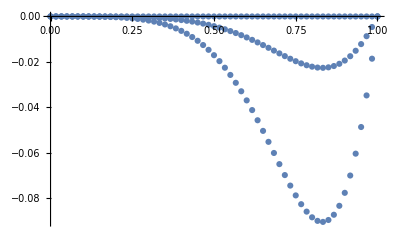

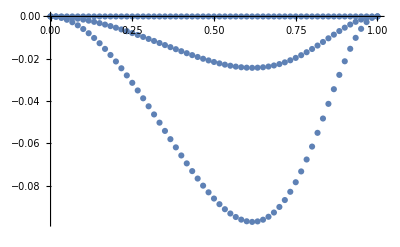

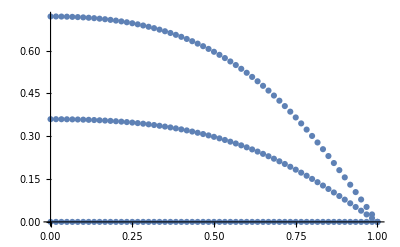

```mathematica
Show[ListPlot[Transpose[{Xrange,f2mat[[1,1;;]]}]],ListPlot[Transpose[{Xrange,f2mat[[16,1;;]]}]],ListPlot[Transpose[{Xrange,f2mat[[31,1;;]]}]],PlotRange->All]

Show[ListPlot[Transpose[{Xrange,m2mat[[1,1;;]]}]],ListPlot[Transpose[{Xrange,m2mat[[16,1;;]]}]],ListPlot[Transpose[{Xrange,m2mat[[31,1;;]]}]],PlotRange->All]

Show[ListPlot[Transpose[{Xrange,ψ1mat[[1,1;;]]}]],ListPlot[Transpose[{Xrange,ψ1mat[[16,1;;]]}]],ListPlot[Transpose[{Xrange,ψ1mat[[31,1;;]]}]],PlotRange->All]
```

## ζ^2 Fitting

### f ζ^2 Fitting

#### y^n Order Determination: Local x(midpoint) location

{51}

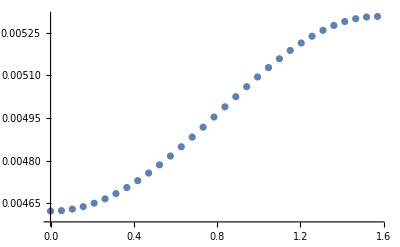

{0,2,4,6,8,10,12,14}

0.997456214836985

0.999999265174093

0.999999999771267

0.999999999966159

0.999999999967818

0.999999999968056

0.999999999967281

0.99999999996748

```mathematica
maxfpos=Ordering[Abs[u0zeta2[[Length[Yrange],1;;]]],-1]
maxfYXdata=Transpose[{Ymat[[1;;,maxfpos]]//Flatten,-u0zeta2[[1;;,maxfpos]]//Flatten}];
ListPlot[maxfYXdata]
yN={0,2,4,6,8,10,12,14}
Ynstr="yj LegendreP[j,Cos[y]]";
coeffn="{yj}";
Ftemp=0;
ctemp = {};
u0maxXFitFunc={};
u0maxXcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]];coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp; u0maxXFitFunc=Join[u0maxXFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u0maxXcoeffFitFunc=Join[u0maxXcoeffFitFunc,{ctemp}],{i,yN}]

u0maxXFit=Table[0,{i,Length[u0maxXFitFunc]}];
Do[u0maxXFit[[i]]=NonlinearModelFit[maxfYXdata,u0maxXFitFunc[[i]],u0maxXcoeffFitFunc[[i]],{y},PrecisionGoal->5,AccuracyGoal->5]; Print[NumberForm[u0maxXFit[[i]]["AdjustedRSquared"],16]],{i,Length[u0maxXFitFunc]}]
```

From this we notice that the R^2value saturates at n=6, with R^2=0.999999999942649

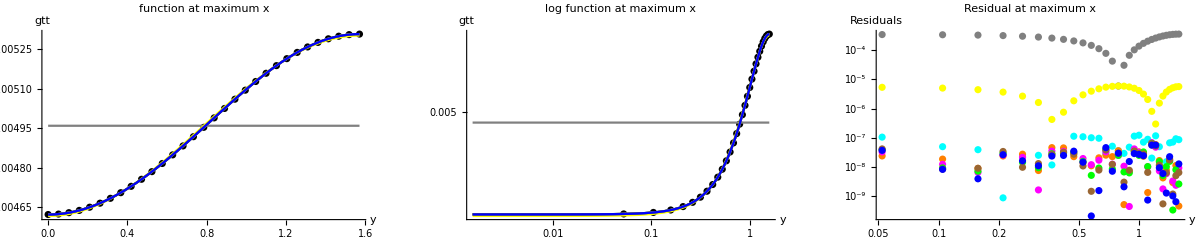

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
maxfXPlot=Table[0,{i,Length[u0maxXFit]+1}];
maxfXPlot[[1]]=ListPlot[maxfYXdata,PlotStyle->Black];
Do[maxfXPlot[[i+1]]=Plot[Normal[u0maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u0maxXFit]}]

maxfXLogPlot=Table[0,{i,Length[u0maxXFit]+1}];
maxfXLogPlot[[1]]=ListLogLogPlot[maxfYXdata,PlotStyle->Black];
Do[maxfXLogPlot[[i+1]]=LogLogPlot[Normal[u0maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u0maxXFit]}]

maxfXRes=Table[0,{i,Length[u0maxXFit]}];
Do[maxfXRes[[i]]=ListLogLogPlot[Transpose[{Ymat[[1;;,maxfpos]]//Flatten,Abs[u0maxXFit[[i]]["FitResiduals"]]}],PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u0maxXFit]}]


Show[GraphicsGrid[{{Show[maxfXPlot,AxesLabel->{y,gtt},PlotLabel->"function at maximum x",PlotRange->All], Show[maxfXLogPlot,AxesLabel->{y,gtt},PlotLabel->"log function at maximum x",PlotRange->All], Show[maxfXRes,AxesLabel->{y,"Residuals"},PlotLabel->"Residual at maximum x",PlotRange->All]}}],ImageSize->1200]
```

The orange residuals on the right above plot correspond to r=6 which is roughly when the residual no longer improves by adding higher orders

#### x^n Order Determination (local y-fit): Order: P_6 (midpoint estimation)

```mathematica
xN={0,1,2,3,4,5,6,7,8,9,10,11,12,13} 
Ynstr="(LegendreP[0,Cos[y]] aj00 + LegendreP[2,Cos[y]] aj02 + LegendreP[4,Cos[y]] aj04 + LegendreP[6,Cos[y]] aj06)";
coeffn="{aj00,aj02,aj04,aj06}";
Xnstr="x^2 (-1+x) x^j";
Ftemp=0;
ctemp = {};
u0XFitFunc={};
u0XcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u0XFitFunc=Join[u0XFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u0XcoeffFitFunc=Join[u0XcoeffFitFunc,{ctemp}],{i,xN}]

u0XFit=Table[0,{i,Length[u0XFitFunc]}];
Do[u0XFit[[i]]=NonlinearModelFit[u0zeta2pts,u0XFitFunc[[i]],u0XcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u0XFit[[i]]["AdjustedRSquared"],16]],{i,Length[u0XFitFunc]}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13}

0.6965061756081353

0.954672549865221

0.997156123471508

0.999927750571115

0.999945903480087

0.999984883645446

0.999998396576369

0.999999764296119

0.999999855801861

0.999999947716374

0.999999988943344

0.999999998026078

0.999999999043266

0.999999999067805

Here n=12

{1,16,31}

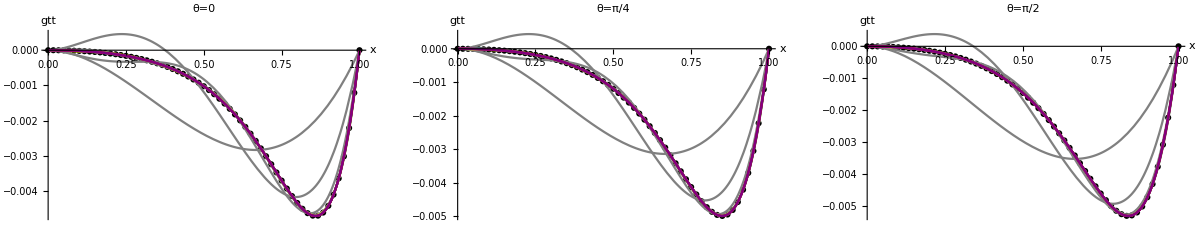

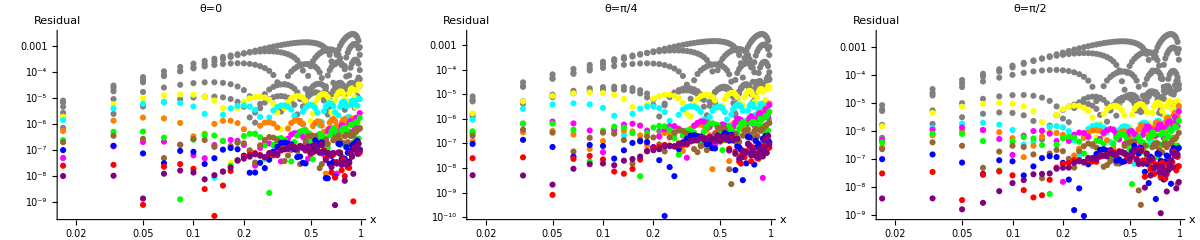

```mathematica
Xcolors={Black,Gray,Gray,Gray,Gray,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u0XPlotY=Table[0,{i,Length[u0XFit]+1},{j,Length[Yplot]}];
Do[u0XPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u0zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u0XPlotY[[i+1,j]]=Plot[u0XFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u0XFit]}]
Show[GraphicsGrid[{{Show[u0XPlotY[[1;;,1]],AxesLabel->{x,gtt},PlotLabel->"θ=0",PlotRange->All],Show[u0XPlotY[[1;;,2]],AxesLabel->{x,gtt},PlotLabel->"θ=π/4",PlotRange->All],Show[u0XPlotY[[1;;,3]],AxesLabel->{x,gtt},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u0XFitRes=Table[0,{i,Length[u0XFit]}];
Do[u0XFitRes[[i]]=Partition[u0XFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u0XFit]}]
u0XResY=Table[0,{i,Length[u0XFit]},{j,Length[Yplot]}];

Do[Do[u0XResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u0XFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u0XFit]}]
Show[GraphicsGrid[{{Show[u0XResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u0XResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u0XResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

Visual verification on bottom-right plot where n=12 is the red residual

#### y^n Order Determination (global x-fit): Order: x^12

```mathematica
yN={0,2,4,6,8,10,12}
Xnstr="x^2(-1+x)(a00j + x^1 a01j + x^2 a02j + x^3 a03j + x^4 a04j + x^5 a05j + x^6 a06j + x^7 a07j + x^8 a08j + x^9 a09j + x^10 a10j + x^11 a11j + x^12 a12j)";
coeffn="{a00j,a01j,a02j,a03j,a04j,a05j,a06j,a07j,a08j,a09j,a10j,a11j,a12j}";
Ynstr="LegendreP[j,Cos[y]]";
Ftemp=0;
ctemp = {};
u0YFitFunc={};
u0YcoeffFitFunc={};

Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u0YFitFunc=Join[u0YFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u0YcoeffFitFunc=Join[u0YcoeffFitFunc,{ctemp}],{i,yN}]
(* To switch between x^n and y^n,  switch u#X... to u#Y... and change Do[...,{i,xN}] to Do[...,{i,yN}] *)

u0YFit=Table[0,{i,Length[u0YFitFunc]}];
Do[u0YFit[[i]]=NonlinearModelFit[u0zeta2pts,u0YFitFunc[[i]],u0YcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u0YFit[[i]]["AdjustedRSquared"],16]],{i,Length[u0YFitFunc]}]
```

{0,2,4,6,8,10,12}

0.995206651295299

0.999981619011536

0.999999902442583

0.999999999043266

0.999999999612825

0.999999999614069

0.999999999612439

This is just verification, we determined y^6 was the saturation point only from a fit at the location where u_0 was maximum. So in that case we had a 1-dimensional fit to make. In this case, we find the y^n value for a global fit on the x-dimension. We find that n=8 is a slightly better fit so we will use that

{1,16,31}

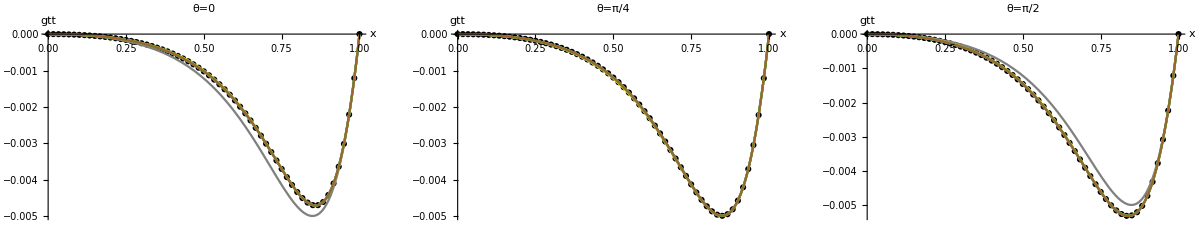

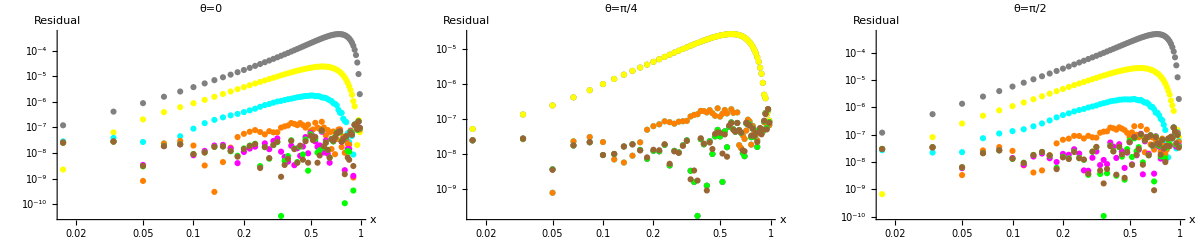

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u0YPlotY=Table[0,{i,Length[u0YFit]+1},{j,Length[Yplot]}];
Do[u0YPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u0zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u0YPlotY[[i+1,j]]=Plot[u0YFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u0YFit]}]
Show[GraphicsGrid[{{Show[u0YPlotY[[1;;,1]],AxesLabel->{x,gtt},PlotLabel->"θ=0",PlotRange->All],Show[u0YPlotY[[1;;,2]],AxesLabel->{x,gtt},PlotLabel->"θ=π/4",PlotRange->All],Show[u0YPlotY[[1;;,3]],AxesLabel->{x,gtt},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u0YFitRes=Table[0,{i,Length[u0YFit]}];
Do[u0YFitRes[[i]]=Partition[u0YFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u0YFit]}]
u0YResY=Table[0,{i,Length[u0YFit]},{j,Length[Yplot]}];
Do[Do[u0YResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u0YFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u0YFit]}]

Show[GraphicsGrid[{{Show[u0YResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u0YResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u0YResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

As explained above, n=8 is the magenta residual

#### Best Fit Calculation: Order: P_8, x^12, u0YFitFunc[[5]]

```mathematica
u0FitFunc=u0YFitFunc[[5]]
u0coeffFitFunc=u0YcoeffFitFunc[[5]];
fullu0fit=NonlinearModelFit[u0zeta2pts,u0FitFunc,u0coeffFitFunc,{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
Normal[fullu0fit];
fullu0fit["BestFitParameters"]
NumberForm[fullu0fit["AdjustedRSquared"],16]
fullu0fit["ParameterTable"];
fullu0fit["ANOVATable"]
```

(-1+x) x^2 (a0000+a0100 x+a0200 x^2+a0300 x^3+a0400 x^4+a0500 x^5+a0600 x^6+a0700 x^7+a0800 x^8+a0900 x^9+a1000 x^10+a1100 x^11+a1200 x^12)+1/2 (-1+x) x^2 (a0002+a0102 x+a0202 x^2+a0302 x^3+a0402 x^4+a0502 x^5+a0602 x^6+a0702 x^7+a0802 x^8+a0902 x^9+a1002 x^10+a1102 x^11+a1202 x^12) (-1+3 Cos[y]^2)+1/8 (-1+x) x^2 (a0004+a0104 x+a0204 x^2+a0304 x^3+a0404 x^4+a0504 x^5+a0604 x^6+a0704 x^7+a0804 x^8+a0904 x^9+a1004 x^10+a1104 x^11+a1204 x^12) (3-30 Cos[y]^2+35 Cos[y]^4)+1/16 (-1+x) x^2 (a0006+a0106 x+a0206 x^2+a0306 x^3+a0406 x^4+a0506 x^5+a0606 x^6+a0706 x^7+a0806 x^8+a0906 x^9+a1006 x^10+a1106 x^11+a1206 x^12) (-5+105 Cos[y]^2-315 Cos[y]^4+231 Cos[y]^6)+1/128 (-1+x) x^2 (a0008+a0108 x+a0208 x^2+a0308 x^3+a0408 x^4+a0508 x^5+a0608 x^6+a0708 x^7+a0808 x^8+a0908 x^9+a1008 x^10+a1108 x^11+a1208 x^12) (35-1260 Cos[y]^2+6930 Cos[y]^4-12012 Cos[y]^6+6435 Cos[y]^8)

{a0000→0.00259415,a0100→-0.00838604,a0200→0.276629,a0300→-2.99656,a0400→20.8909,a0500→-95.7186,a0600→300.938,a0700→-658.781,a0800→1003.93,a0900→-1044.44,a1000→707.438,a1100→-281.127,a1200→49.6745,a0002→-0.000646711,a0102→0.0000692154,a0202→-0.0245956,a0302→0.203645,a0402→-1.15033,a0502→4.04693,a0602→-9.32451,a0702→13.9145,a0802→-12.947,a0902→6.93172,a1002→-1.94175,a1102→0.543771,a1202→-0.251764,a0004→0.000199077,a0104→-0.000721655,a0204→0.0215893,a0304→-0.229595,a0404→1.5296,a0504→-6.72759,a0604→20.2102,a0704→-42.1455,a0804→60.9249,a0904→-59.8637,a1004→38.1174,a1104→-14.165,a1204→2.32819,a0006→-0.0000229613,a0106→-0.000117178,a0206→0.000617218,a0306→0.00015902,a0406→-0.0426082,a0506→0.34787,a0606→-1.4421,a0706→3.66418,a0806→-6.0181,a0906→6.42987,a1006→-4.33057,a1106→1.67548,a1206→-0.284655,a0008→-3.08651×10^-6,a0108→0.000285419,a0208→-0.0051789,a0308→0.0517026,a0408→-0.315757,a0508→1.25767,a0608→-3.38108,a0708→6.21703,a0808→-7.78542,a0908→6.47877,a1008→-3.38906,a1108→0.990376,a1208→-0.119322}

0.999999999612825

| DF | SS | MS
Model | 65 | 1.16102×10^8 | 1.78618×10^6
Error | 1826 | 0.0434065 | 0.0000237714
Uncorrected Total | 1891 | 1.16102×10^8 | 
Corrected Total | 1890 | 5.81254×10^7 |

#### Best Fit Comparison

```mathematica
u0fitres=Partition[fullu0fit["FitResiduals"],Length[Xrange]];
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]};
u0Plot=Table[0,5,{i,Length[Yplot]}];

Do[u0Plot[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u0zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u0Plot[[2,j]]=Plot[fullu0fit["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u0Plot[[3,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u0zeta2[[Yplot[[j]],1;;]]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u0Plot[[4,j]]=LogLogPlot[Abs[fullu0fit["Function"][Yrange[[Yplot[[j]]]],x]],{x,0.01,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u0Plot[[5,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u0fitres[[Yplot[[j]],1;;]]]}],PlotStyle->Red],{j,Length[Yplot]}];
```

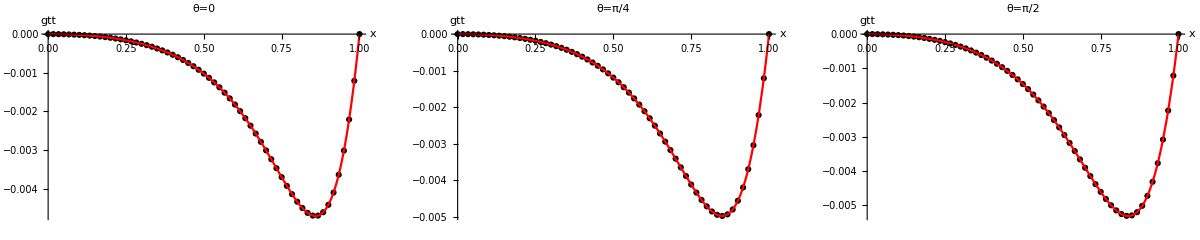

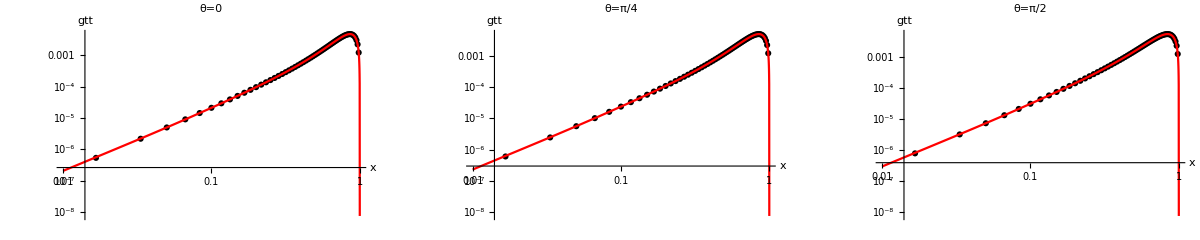

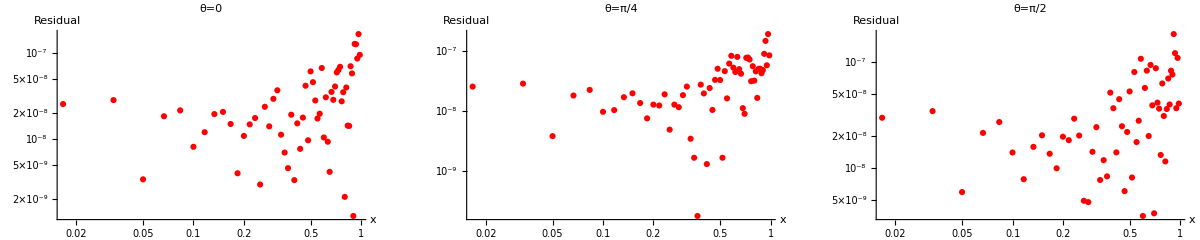

```mathematica
Show[GraphicsGrid[{{Show[u0Plot[[1;;2,1]],AxesLabel->{x,gtt},PlotLabel->"θ=0",PlotRange->All],Show[u0Plot[[1;;2,2]],AxesLabel->{x,gtt},PlotLabel->"θ=π/4",PlotRange->All],Show[u0Plot[[1;;2,3]],AxesLabel->{x,gtt},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u0Plot[[3;;4,1]],AxesLabel->{x,gtt},PlotLabel->"θ=0",PlotRange->All],Show[u0Plot[[3;;4,2]],AxesLabel->{x,gtt},PlotLabel->"θ=π/4",PlotRange->All],Show[u0Plot[[3;;4,3]],AxesLabel->{x,gtt},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u0Plot[[5,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All],Show[u0Plot[[5,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All],Show[u0Plot[[5,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

### m ζ^2 Fitting

#### y^n Order Determination: Local x(midpoint) location

{38}

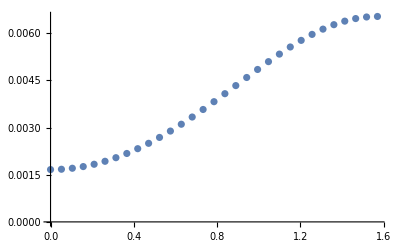

{0,2,4,6,8,10,12,14}

0.832076613128968

0.999441955160808

0.999997966952133

0.999999992957537

0.999999999827589

0.999999999825653

0.99999999982171

0.9999999998153

```mathematica
maxmpos=Ordering[Abs[u1zeta2[[Length[Yrange],1;;]]],-1]
maxmYXdata=Transpose[{Ymat[[1;;,maxmpos]]//Flatten,-u1zeta2[[1;;,maxmpos]]//Flatten}];
ListPlot[maxmYXdata]
yN={0,2,4,6,8,10,12,14}
Ynstr="yj LegendreP[j,Cos[y]]";
coeffn="{yj}";
Ftemp=0;
ctemp = {};
u1maxXFitFunc={};
u1maxXcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]];coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp; u1maxXFitFunc=Join[u1maxXFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u1maxXcoeffFitFunc=Join[u1maxXcoeffFitFunc,{ctemp}],{i,yN}]

u1maxXFit=Table[0,{i,Length[u1maxXFitFunc]}];
Do[u1maxXFit[[i]]=NonlinearModelFit[maxmYXdata,u1maxXFitFunc[[i]],u1maxXcoeffFitFunc[[i]],{y},PrecisionGoal->5,AccuracyGoal->5]; Print[NumberForm[u1maxXFit[[i]]["AdjustedRSquared"],16]],{i,Length[u1maxXFitFunc]}]
```

From this we notice that the R^2value saturates at n=8, with R^2=0.999999999827589

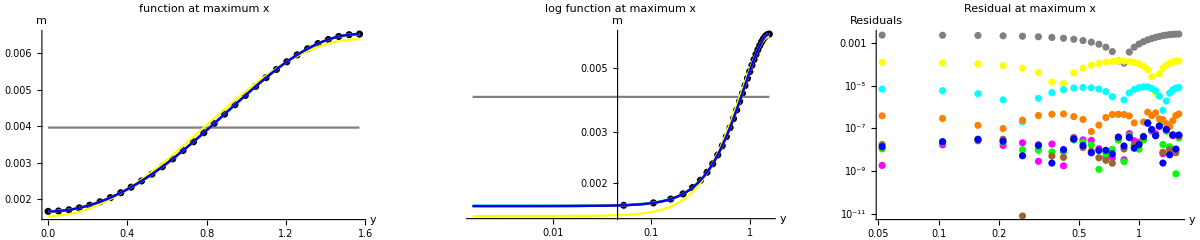

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
maxmXPlot=Table[0,{i,Length[u1maxXFit]+1}];
maxmXPlot[[1]]=ListPlot[maxmYXdata,PlotStyle->Black];
Do[maxmXPlot[[i+1]]=Plot[Normal[u1maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u1maxXFit]}]

maxmXLogPlot=Table[0,{i,Length[u1maxXFit]+1}];
maxmXLogPlot[[1]]=ListLogLogPlot[maxmYXdata,PlotStyle->Black];
Do[maxmXLogPlot[[i+1]]=LogLogPlot[Normal[u1maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u1maxXFit]}]

maxmXRes=Table[0,{i,Length[u1maxXFit]}];
Do[maxmXRes[[i]]=ListLogLogPlot[Transpose[{Ymat[[1;;,maxmpos]]//Flatten,Abs[u1maxXFit[[i]]["FitResiduals"]]}],PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u1maxXFit]}]


Show[GraphicsGrid[{{Show[maxmXPlot,AxesLabel->{y,m},PlotLabel->"function at maximum x",PlotRange->All], Show[maxmXLogPlot,AxesLabel->{y,m},PlotLabel->"log function at maximum x",PlotRange->All], Show[maxmXRes,AxesLabel->{y,"Residuals"},PlotLabel->"Residual at maximum x",PlotRange->All]}}],ImageSize->1200]
```

The magenta residuals on the right above plot correspond to r=8 which is roughly when the residual no longer improves by adding higher orders

#### x^n Order Determination (local y-fit): Order: P_8 (midpoint estimation)

```mathematica
xN={0,1,2,3,4,5,6,7,8,9,10,11,12,13} 
Ynstr="(LegendreP[0,Cos[y]] aj00 + LegendreP[2,Cos[y]] aj02 + LegendreP[4,Cos[y]] aj04 + LegendreP[6,Cos[y]] aj06 + LegendreP[8,Cos[y]] aj08)";
coeffn="{aj00,aj02,aj04,aj06,aj08}";
Xnstr="x^2 (-1+x)^2 x^j";
Ftemp=0;
ctemp = {};
u1XFitFunc={};
u1XcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u1XFitFunc=Join[u1XFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u1XcoeffFitFunc=Join[u1XcoeffFitFunc,{ctemp}],{i,xN}]

u1XFit=Table[0,{i,Length[u1XFitFunc]}];
Do[u1XFit[[i]]=NonlinearModelFit[u1zeta2pts,u1XFitFunc[[i]],u1XcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u1XFit[[i]]["AdjustedRSquared"],16]],{i,Length[u1XFitFunc]}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13}

0.908013602730315

0.993179801054302

0.999809525825727

0.999966299218683

0.999979271676614

0.999994679085826

0.999999203612862

0.999999932794355

0.999999995502807

0.999999996592159

0.999999997297229

0.999999998108581

0.999999998535688

0.99999999874044

Here n=8

{1,16,31}

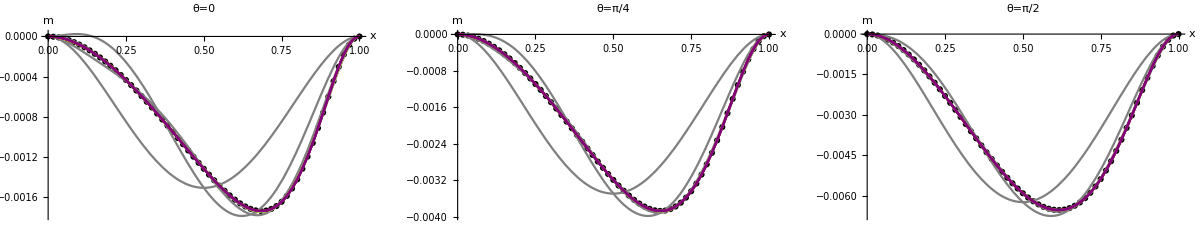

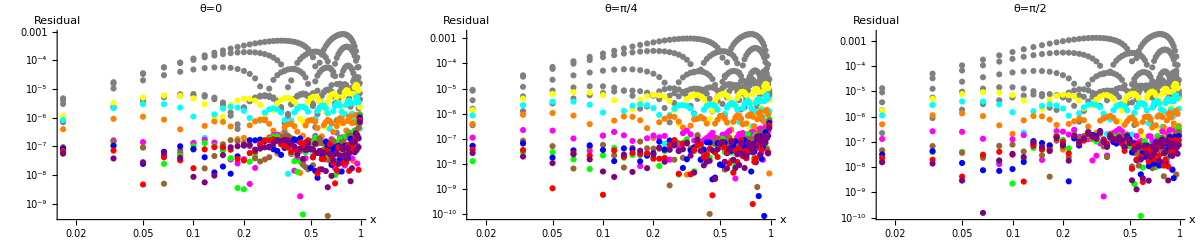

```mathematica
Xcolors={Black,Gray,Gray,Gray,Gray,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u1XPlotY=Table[0,{i,Length[u1XFit]+1},{j,Length[Yplot]}];
Do[u1XPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u1zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u1XPlotY[[i+1,j]]=Plot[u1XFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u1XFit]}]
Show[GraphicsGrid[{{Show[u1XPlotY[[1;;,1]],AxesLabel->{x,m},PlotLabel->"θ=0",PlotRange->All],Show[u1XPlotY[[1;;,2]],AxesLabel->{x,m},PlotLabel->"θ=π/4",PlotRange->All],Show[u1XPlotY[[1;;,3]],AxesLabel->{x,m},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u1XFitRes=Table[0,{i,Length[u1XFit]}];
Do[u1XFitRes[[i]]=Partition[u1XFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u1XFit]}]
u1XResY=Table[0,{i,Length[u1XFit]},{j,Length[Yplot]}];

Do[Do[u1XResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u1XFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u1XFit]}]
Show[GraphicsGrid[{{Show[u1XResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u1XResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u1XResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

Visual verification on bottom-right plot where n=8 is the magenta residual

#### y^n Order Determination (global x-fit): Order: x^8

```mathematica
yN={0,2,4,6,8,10,12}
Xnstr="x^2(-1+x)^2(a00j + x^1 a01j + x^2 a02j + x^3 a03j + x^4 a04j + x^5 a05j + x^6 a06j + x^7 a07j + x^8 a08j)";
coeffn="{a00j,a01j,a02j,a03j,a04j,a05j,a06j,a07j,a08j}";
Ynstr="LegendreP[j,Cos[y]]";
Ftemp=0;
ctemp = {};
u1YFitFunc={};
u1YcoeffFitFunc={};

Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u1YFitFunc=Join[u1YFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u1YcoeffFitFunc=Join[u1YcoeffFitFunc,{ctemp}],{i,yN}]
(* To switch between x^n and y^n,  switch u#X... to u#Y... and change Do[...,{i,xN}] to Do[...,{i,yN}] *)

u1YFit=Table[0,{i,Length[u1YFitFunc]}];
Do[u1YFit[[i]]=NonlinearModelFit[u1zeta2pts,u1YFitFunc[[i]],u1YcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u1YFit[[i]]["AdjustedRSquared"],16]],{i,Length[u1YFitFunc]}]
```

{0,2,4,6,8,10,12}

0.833229107700331

0.998833084873736

0.999991793889271

0.999999937876937

0.999999995502807

0.999999995957478

0.999999995940521

This is just verification, we determined y^8 was the saturation point only from a fit at the location where u_0 was maximum. So in that case we had a 1-dimensional fit to make. In this case, we find the y^n value for a global fit on the x-dimension. We recover that the saturation residual is again n=8

{1,16,31}

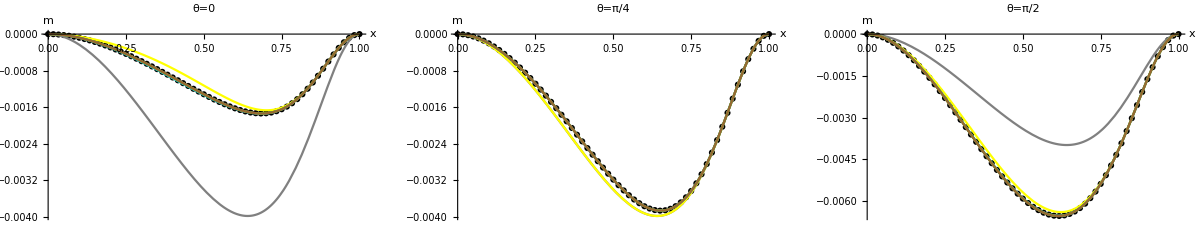

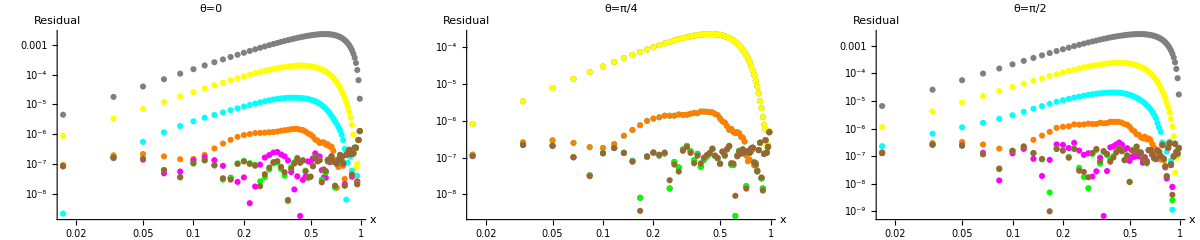

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u1YPlotY=Table[0,{i,Length[u1YFit]+1},{j,Length[Yplot]}];
Do[u1YPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u1zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u1YPlotY[[i+1,j]]=Plot[u1YFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u1YFit]}]
Show[GraphicsGrid[{{Show[u1YPlotY[[1;;,1]],AxesLabel->{x,m},PlotLabel->"θ=0",PlotRange->All],Show[u1YPlotY[[1;;,2]],AxesLabel->{x,m},PlotLabel->"θ=π/4",PlotRange->All],Show[u1YPlotY[[1;;,3]],AxesLabel->{x,m},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u1YFitRes=Table[0,{i,Length[u1YFit]}];
Do[u1YFitRes[[i]]=Partition[u1YFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u1YFit]}]
u1YResY=Table[0,{i,Length[u1YFit]},{j,Length[Yplot]}];
Do[Do[u1YResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u1YFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u1YFit]}]

Show[GraphicsGrid[{{Show[u1YResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u1YResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u1YResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

As explained above, n=8 is the magenta residual

#### Best Fit Calculation: Order: P_8, x^8, u0YFitFunc[[5]]

```mathematica
u1FitFunc=u1YFitFunc[[5]]
u1coeffFitFunc=u1YcoeffFitFunc[[5]];
fullu1fit=NonlinearModelFit[u1zeta2pts,u1FitFunc,u1coeffFitFunc,{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
Normal[fullu1fit];
fullu1fit["BestFitParameters"]
NumberForm[fullu1fit["AdjustedRSquared"],16]
fullu1fit["ParameterTable"];
fullu1fit["ANOVATable"]
```

(-1+x)^2 x^2 (a0000+a0100 x+a0200 x^2+a0300 x^3+a0400 x^4+a0500 x^5+a0600 x^6+a0700 x^7+a0800 x^8)+1/2 (-1+x)^2 x^2 (a0002+a0102 x+a0202 x^2+a0302 x^3+a0402 x^4+a0502 x^5+a0602 x^6+a0702 x^7+a0802 x^8) (-1+3 Cos[y]^2)+1/8 (-1+x)^2 x^2 (a0004+a0104 x+a0204 x^2+a0304 x^3+a0404 x^4+a0504 x^5+a0604 x^6+a0704 x^7+a0804 x^8) (3-30 Cos[y]^2+35 Cos[y]^4)+1/16 (-1+x)^2 x^2 (a0006+a0106 x+a0206 x^2+a0306 x^3+a0406 x^4+a0506 x^5+a0606 x^6+a0706 x^7+a0806 x^8) (-5+105 Cos[y]^2-315 Cos[y]^4+231 Cos[y]^6)+1/128 (-1+x)^2 x^2 (a0008+a0108 x+a0208 x^2+a0308 x^3+a0408 x^4+a0508 x^5+a0608 x^6+a0708 x^7+a0808 x^8) (35-1260 Cos[y]^2+6930 Cos[y]^4-12012 Cos[y]^6+6435 Cos[y]^8)

{a0000→-0.0313518,a0100→-0.0567903,a0200→0.267201,a0300→-1.98868,a0400→7.18225,a0500→-16.1566,a0600→21.4264,a0700→-15.7182,a0800→4.91785,a0002→0.0287121,a0102→0.0351248,a0202→-0.0522703,a0302→0.472036,a0402→-1.6461,a0502→3.626,a0602→-4.76372,a0702→3.49212,a0802→-1.10998,a0004→-0.00645619,a0104→-0.00592775,a0204→0.000831269,a0304→-0.00290039,a0404→0.181476,a0504→-0.627386,a0604→1.19946,a0704→-1.15238,a0804→0.41371,a0006→0.000837572,a0106→0.0000462419,a0206→0.00850046,a0306→-0.0607549,a0406→0.201857,a0506→-0.4223,a0606→0.505433,a0706→-0.304366,a0806→0.0706748,a0008→-0.0000953757,a0108→0.0000788313,a0208→-0.00193405,a0308→0.0132203,a0408→-0.0445096,a0508→0.0946676,a0608→-0.121257,a0708→0.0825362,a0808→-0.0227201}

0.999999995502807

| DF | SS | MS
Model | 45 | 1.3695×10^8 | 3.04334×10^6
Error | 1846 | 0.601236 | 0.000325696
Uncorrected Total | 1891 | 1.3695×10^8 | 
Corrected Total | 1890 | 6.03384×10^7 |

#### Best Fit Comparison

```mathematica
u1fitres=Partition[fullu1fit["FitResiduals"],Length[Xrange]];
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]};
u1Plot=Table[0,5,{i,Length[Yplot]}];

Do[u1Plot[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u1zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u1Plot[[2,j]]=Plot[fullu1fit["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u1Plot[[3,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u1zeta2[[Yplot[[j]],1;;]]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u1Plot[[4,j]]=LogLogPlot[Abs[fullu1fit["Function"][Yrange[[Yplot[[j]]]],x]],{x,0.01,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u1Plot[[5,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u1fitres[[Yplot[[j]],1;;]]]}],PlotStyle->Red],{j,Length[Yplot]}];
```

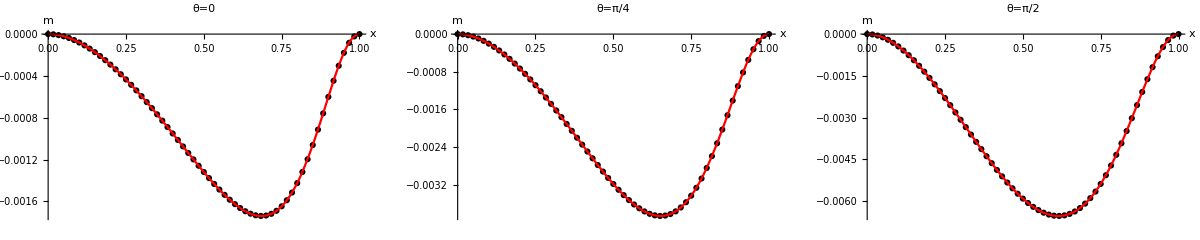

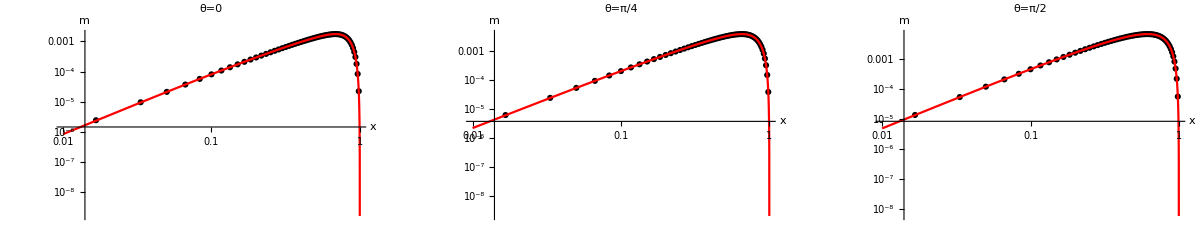

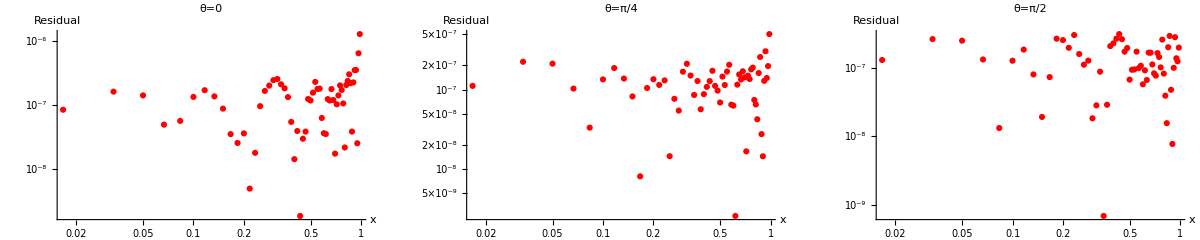

```mathematica
Show[GraphicsGrid[{{Show[u1Plot[[1;;2,1]],AxesLabel->{x,m},PlotLabel->"θ=0",PlotRange->All],Show[u1Plot[[1;;2,2]],AxesLabel->{x,m},PlotLabel->"θ=π/4",PlotRange->All],Show[u1Plot[[1;;2,3]],AxesLabel->{x,m},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u1Plot[[3;;4,1]],AxesLabel->{x,m},PlotLabel->"θ=0",PlotRange->All],Show[u1Plot[[3;;4,2]],AxesLabel->{x,m},PlotLabel->"θ=π/4",PlotRange->All],Show[u1Plot[[3;;4,3]],AxesLabel->{x,m},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u1Plot[[5,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All],Show[u1Plot[[5,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All],Show[u1Plot[[5,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

### l ζ^2 Fitting

#### y^n Order Determination: Local x(midpoint) location

{43}

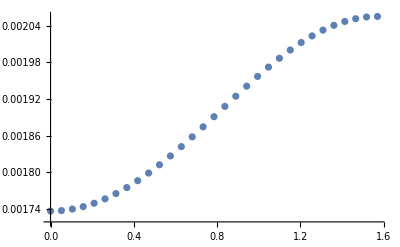

{0,2,4,6,8,10,12,14}

0.996210328186909

0.99999912503292

0.999999992162756

0.999999999723791

0.999999999768821

0.999999999762426

0.99999999975254

0.999999999781873

```mathematica
maxlpos=Ordering[Abs[u2zeta2[[Length[Yrange],1;;]]],-1]
maxlYXdata=Transpose[{Ymat[[1;;,maxlpos]]//Flatten,-u2zeta2[[1;;,maxlpos]]//Flatten}];
ListPlot[maxlYXdata]
yN={0,2,4,6,8,10,12,14}
Ynstr="yj LegendreP[j,Cos[y]]";
coeffn="{yj}";
Ftemp=0;
ctemp = {};
u2maxXFitFunc={};
u2maxXcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]];coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp; u2maxXFitFunc=Join[u2maxXFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u2maxXcoeffFitFunc=Join[u2maxXcoeffFitFunc,{ctemp}],{i,yN}]

u2maxXFit=Table[0,{i,Length[u2maxXFitFunc]}];
Do[u2maxXFit[[i]]=NonlinearModelFit[maxlYXdata,u2maxXFitFunc[[i]],u2maxXcoeffFitFunc[[i]],{y},PrecisionGoal->5,AccuracyGoal->5]; Print[NumberForm[u2maxXFit[[i]]["AdjustedRSquared"],16]],{i,Length[u2maxXFitFunc]}]
```

From this we notice that the R^2value saturates at n=6, with R^2=0.999999999723791

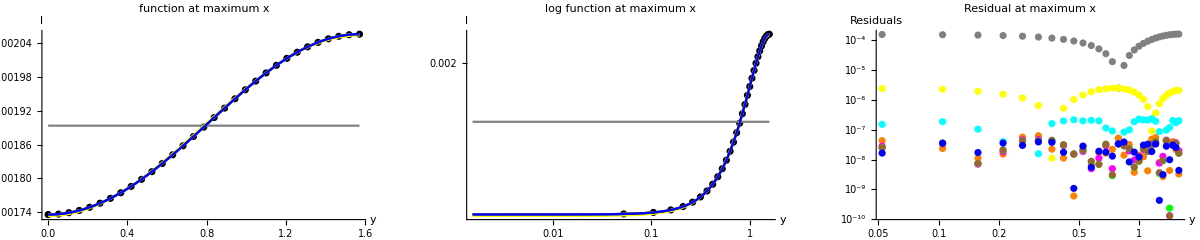

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
maxlXPlot=Table[0,{i,Length[u2maxXFit]+1}];
maxlXPlot[[1]]=ListPlot[maxlYXdata,PlotStyle->Black];
Do[maxlXPlot[[i+1]]=Plot[Normal[u2maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u2maxXFit]}]

maxlXLogPlot=Table[0,{i,Length[u2maxXFit]+1}];
maxlXLogPlot[[1]]=ListLogLogPlot[maxlYXdata,PlotStyle->Black];
Do[maxlXLogPlot[[i+1]]=LogLogPlot[Normal[u2maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u2maxXFit]}]

maxlXRes=Table[0,{i,Length[u2maxXFit]}];
Do[maxlXRes[[i]]=ListLogLogPlot[Transpose[{Ymat[[1;;,maxlpos]]//Flatten,Abs[u2maxXFit[[i]]["FitResiduals"]]}],PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u2maxXFit]}]


Show[GraphicsGrid[{{Show[maxlXPlot,AxesLabel->{y,l},PlotLabel->"function at maximum x",PlotRange->All], Show[maxlXLogPlot,AxesLabel->{y,l},PlotLabel->"log function at maximum x",PlotRange->All], Show[maxlXRes,AxesLabel->{y,"Residuals"},PlotLabel->"Residual at maximum x",PlotRange->All]}}],ImageSize->1200]
```

The orange residuals on the right above plot correspond to r=6 which is roughly when the residual no longer improves by adding higher orders

#### x^n Order Determination (local y-fit): Order: y^6 (midpoint estimation)

```mathematica
xN={0,1,2,3,4,5,6,7,8,9,10,11,12,13} 
Ynstr="(LegendreP[0,Cos[y]] aj00 + LegendreP[2,Cos[y]] aj02 + LegendreP[4,Cos[y]] aj04 + LegendreP[6,Cos[y]] aj06)";
coeffn="{aj00,aj02,aj04,aj06}";
Xnstr="x^2 (-1+x)^2 x^j";
Ftemp=0;
ctemp = {};
u2XFitFunc={};
u2XcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u2XFitFunc=Join[u2XFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u2XcoeffFitFunc=Join[u2XcoeffFitFunc,{ctemp}],{i,xN}]

u2XFit=Table[0,{i,Length[u2XFitFunc]}];
Do[u2XFit[[i]]=NonlinearModelFit[u2zeta2pts,u2XFitFunc[[i]],u2XcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u2XFit[[i]]["AdjustedRSquared"],16]],{i,Length[u2XFitFunc]}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13}

0.7781747926532995

0.977259768225924

0.999285751825337

0.999828996588786

0.999928848542962

0.999984842570851

0.999998015116889

0.999999805801236

0.999999922494384

0.999999925683494

0.999999930221078

0.999999932566129

0.999999933219684

0.999999933331699

Here n=8

{1,16,31}

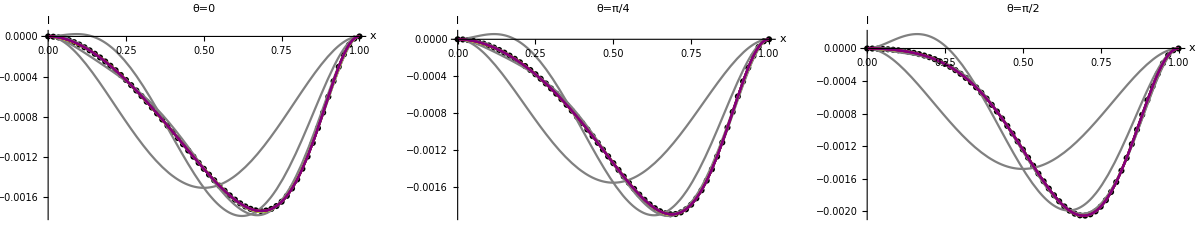

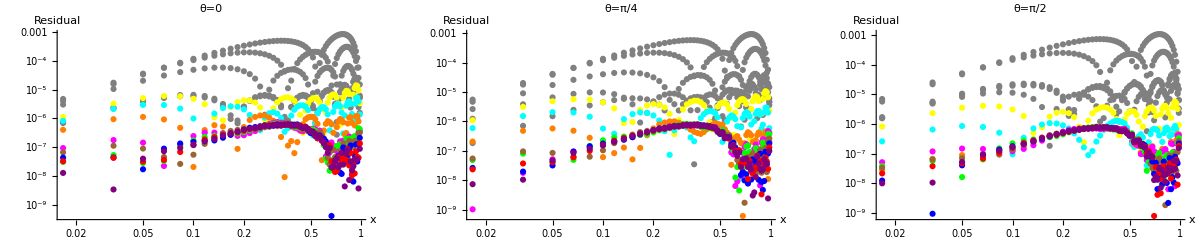

```mathematica
Xcolors={Black,Gray,Gray,Gray,Gray,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u2XPlotY=Table[0,{i,Length[u2XFit]+1},{j,Length[Yplot]}];
Do[u2XPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u2zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u2XPlotY[[i+1,j]]=Plot[u2XFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u2XFit]}]
Show[GraphicsGrid[{{Show[u2XPlotY[[1;;,1]],AxesLabel->{x,l},PlotLabel->"θ=0",PlotRange->All],Show[u2XPlotY[[1;;,2]],AxesLabel->{x,l},PlotLabel->"θ=π/4",PlotRange->All],Show[u2XPlotY[[1;;,3]],AxesLabel->{x,l},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u2XFitRes=Table[0,{i,Length[u2XFit]}];
Do[u2XFitRes[[i]]=Partition[u2XFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u2XFit]}]
u2XResY=Table[0,{i,Length[u2XFit]},{j,Length[Yplot]}];

Do[Do[u2XResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u2XFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u2XFit]}]
Show[GraphicsGrid[{{Show[u2XResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u2XResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u2XResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

Visual verification on bottom-right plot where n=8 is the magenta residual

#### y^n Order Determination (global x-fit): Order: x^8

```mathematica
yN={0,2,4,6,8,10,12}
Xnstr="x^2(-1+x)^2(a00j + x^1 a01j + x^2 a02j + x^3 a03j + x^4 a04j + x^5 a05j + x^6 a06j + x^7 a07j + x^8 a08j)";
coeffn="{a00j,a01j,a02j,a03j,a04j,a05j,a06j,a07j,a08j}";
Ynstr="LegendreP[j,Cos[y]]";
Ftemp=0;
ctemp = {};
u2YFitFunc={};
u2YcoeffFitFunc={};

Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u2YFitFunc=Join[u2YFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u2YcoeffFitFunc=Join[u2YcoeffFitFunc,{ctemp}],{i,yN}]
(* To switch between x^n and y^n,  switch u#X... to u#Y... and change Do[...,{i,xN}] to Do[...,{i,yN}] *)

u2YFit=Table[0,{i,Length[u2YFitFunc]}];
Do[u2YFit[[i]]=NonlinearModelFit[u2zeta2pts,u2YFitFunc[[i]],u2YcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u2YFit[[i]]["AdjustedRSquared"],16]],{i,Length[u2YFitFunc]}]
```

{0,2,4,6,8,10,12}

0.995948803185587

0.999777609685913

0.999995126040748

0.999999922494384

0.999999986883217

0.999999987613574

0.999999987567459

n=8

{1,16,31}

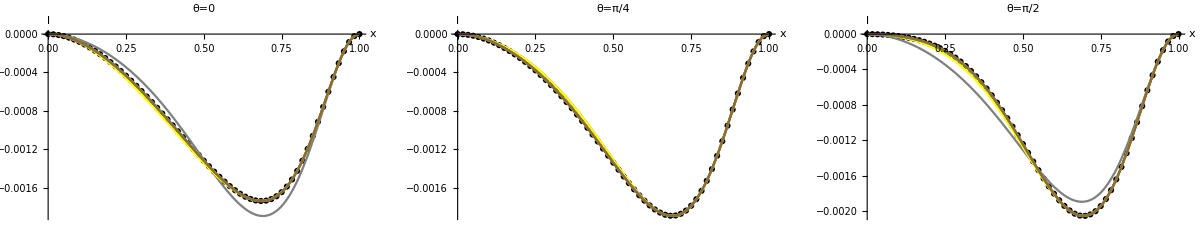

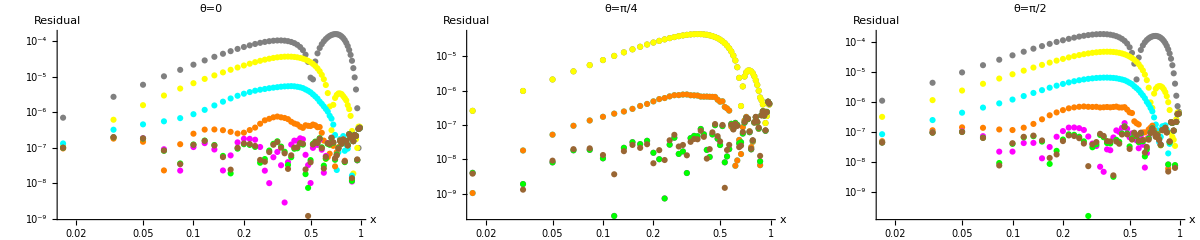

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u2YPlotY=Table[0,{i,Length[u2YFit]+1},{j,Length[Yplot]}];
Do[u2YPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u2zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u2YPlotY[[i+1,j]]=Plot[u2YFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u2YFit]}]
Show[GraphicsGrid[{{Show[u2YPlotY[[1;;,1]],AxesLabel->{x,l},PlotLabel->"θ=0",PlotRange->All],Show[u2YPlotY[[1;;,2]],AxesLabel->{x,l},PlotLabel->"θ=π/4",PlotRange->All],Show[u2YPlotY[[1;;,3]],AxesLabel->{x,l},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u2YFitRes=Table[0,{i,Length[u2YFit]}];
Do[u2YFitRes[[i]]=Partition[u2YFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u2YFit]}]
u2YResY=Table[0,{i,Length[u2YFit]},{j,Length[Yplot]}];
Do[Do[u2YResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u2YFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u2YFit]}]

Show[GraphicsGrid[{{Show[u2YResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u2YResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u2YResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

n=8 is the magenta residual

#### Best Fit Calculation: Order: P_8, x^8, u2YFitFunc[[5]]

```mathematica
u2FitFunc=u2YFitFunc[[5]]
u2coeffFitFunc=u2YcoeffFitFunc[[5]];
fullu2fit=NonlinearModelFit[u2zeta2pts,u2FitFunc,u2coeffFitFunc,{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
Normal[fullu2fit];
fullu2fit["BestFitParameters"]
NumberForm[fullu2fit["AdjustedRSquared"],16]
fullu2fit["ParameterTable"];
fullu2fit["ANOVATable"]
```

(-1+x)^2 x^2 (a0000+a0100 x+a0200 x^2+a0300 x^3+a0400 x^4+a0500 x^5+a0600 x^6+a0700 x^7+a0800 x^8)+1/2 (-1+x)^2 x^2 (a0002+a0102 x+a0202 x^2+a0302 x^3+a0402 x^4+a0502 x^5+a0602 x^6+a0702 x^7+a0802 x^8) (-1+3 Cos[y]^2)+1/8 (-1+x)^2 x^2 (a0004+a0104 x+a0204 x^2+a0304 x^3+a0404 x^4+a0504 x^5+a0604 x^6+a0704 x^7+a0804 x^8) (3-30 Cos[y]^2+35 Cos[y]^4)+1/16 (-1+x)^2 x^2 (a0006+a0106 x+a0206 x^2+a0306 x^3+a0406 x^4+a0506 x^5+a0606 x^6+a0706 x^7+a0806 x^8) (-5+105 Cos[y]^2-315 Cos[y]^4+231 Cos[y]^6)+1/128 (-1+x)^2 x^2 (a0008+a0108 x+a0208 x^2+a0308 x^3+a0408 x^4+a0508 x^5+a0608 x^6+a0708 x^7+a0808 x^8) (35-1260 Cos[y]^2+6930 Cos[y]^4-12012 Cos[y]^6+6435 Cos[y]^8)

{a0000→-0.00548602,a0100→-0.00467957,a0200→-0.0197624,a0300→-0.104526,a0400→0.474557,a0500→-1.76565,a0600→3.15385,a0700→-2.99838,a0800→1.1943,a0002→-0.00435205,a0102→-0.0232348,a0202→0.232356,a0302→-1.38482,a0402→5.16253,a0502→-11.2538,a0602→14.6019,a0702→-10.3942,a0802→3.06422,a0004→0.00186954,a0104→-0.00240962,a0204→0.0446135,a0304→-0.285972,a0404→0.932484,a0504→-1.86245,a0604→2.14705,a0704→-1.26597,a0804→0.290487,a0006→-0.000341898,a0106→0.000163555,a0206→-0.00527038,a0306→0.0389667,a0406→-0.135736,a0506→0.299297,a0606→-0.393488,a0706→0.270871,a0806→-0.0744744,a0008→0.0000459743,a0108→0.0000522349,a0208→-0.000138754,a0308→-0.000577628,a0408→0.00236166,a0508→-0.00815646,a0608→0.0165649,a0708→-0.0151878,a0808→0.00503759}

0.999999986883217

| DF | SS | MS
Model | 45 | 2.25103×10^7 | 500229.
Error | 1846 | 0.288236 | 0.000156141
Uncorrected Total | 1891 | 2.25103×10^7 | 
Corrected Total | 1890 | 8.59963×10^6 |

#### Best Fit Comparison

```mathematica
u2fitres=Partition[fullu2fit["FitResiduals"],Length[Xrange]];
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]};
u2Plot=Table[0,5,{i,Length[Yplot]}];

Do[u2Plot[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u2zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u2Plot[[2,j]]=Plot[fullu2fit["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u2Plot[[3,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u2zeta2[[Yplot[[j]],1;;]]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u2Plot[[4,j]]=LogLogPlot[Abs[fullu2fit["Function"][Yrange[[Yplot[[j]]]],x]],{x,0.01,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u2Plot[[5,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u2fitres[[Yplot[[j]],1;;]]]}],PlotStyle->Red],{j,Length[Yplot]}];
```

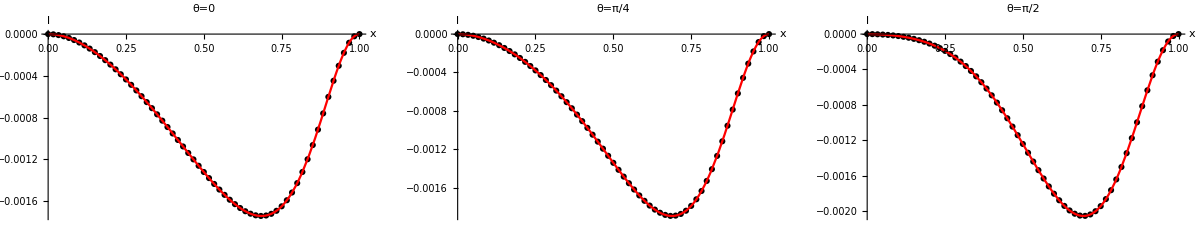

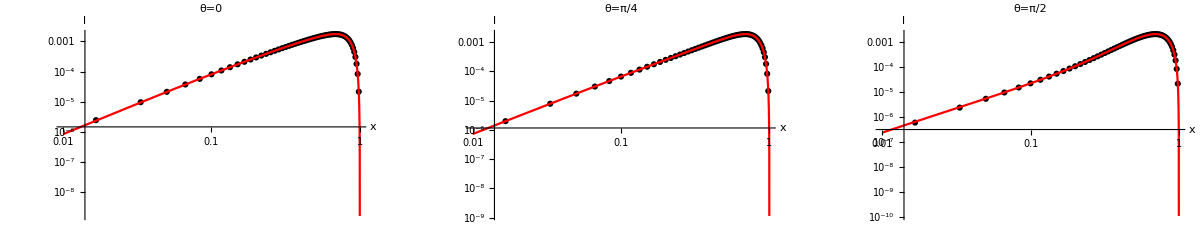

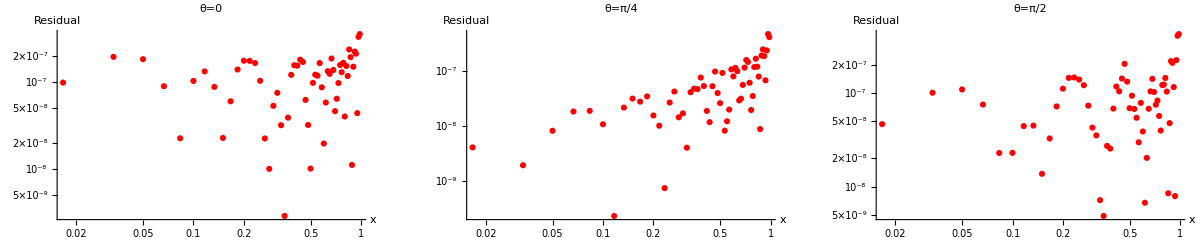

```mathematica
Show[GraphicsGrid[{{Show[u2Plot[[1;;2,1]],AxesLabel->{x,l},PlotLabel->"θ=0",PlotRange->All],Show[u2Plot[[1;;2,2]],AxesLabel->{x,l},PlotLabel->"θ=π/4",PlotRange->All],Show[u2Plot[[1;;2,3]],AxesLabel->{x,l},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u2Plot[[3;;4,1]],AxesLabel->{x,l},PlotLabel->"θ=0",PlotRange->All],Show[u2Plot[[3;;4,2]],AxesLabel->{x,l},PlotLabel->"θ=π/4",PlotRange->All],Show[u2Plot[[3;;4,3]],AxesLabel->{x,l},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u2Plot[[5,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All],Show[u2Plot[[5,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All],Show[u2Plot[[5,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

### ω ζ^2 Fitting

#### y^n Order Determination: Local x(midpoint) location

{50}

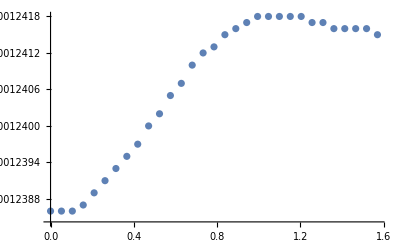

{0,2,4,6,8,10,12,14}

0.999999062892144

0.999999850696428

0.999999999120814

0.999999999316315

0.999999999290085

0.999999999267619

0.999999999237135

0.999999999221822

```mathematica
maxopos=Ordering[Abs[u3zeta2[[Length[Yrange],1;;]]],-1]
maxoYXdata=Transpose[{Ymat[[1;;,maxopos]]//Flatten,u3zeta2[[1;;,maxopos]]//Flatten}];
ListPlot[maxoYXdata]
yN={0,2,4,6,8,10,12,14}
Ynstr="yj LegendreP[j,Cos[y]]";
coeffn="{yj}";
Ftemp=0;
ctemp = {};
u3maxXFitFunc={};
u3maxXcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]];coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp; u3maxXFitFunc=Join[u3maxXFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u3maxXcoeffFitFunc=Join[u3maxXcoeffFitFunc,{ctemp}],{i,yN}]

u3maxXFit=Table[0,{i,Length[u3maxXFitFunc]}];
Do[u3maxXFit[[i]]=NonlinearModelFit[maxoYXdata,u3maxXFitFunc[[i]],u3maxXcoeffFitFunc[[i]],{y},PrecisionGoal->5,AccuracyGoal->5]; Print[NumberForm[u3maxXFit[[i]]["AdjustedRSquared"],16]],{i,Length[u3maxXFitFunc]}]
```

From this we notice that the R^2value saturates at n=4, with R^2=0.999999999120814

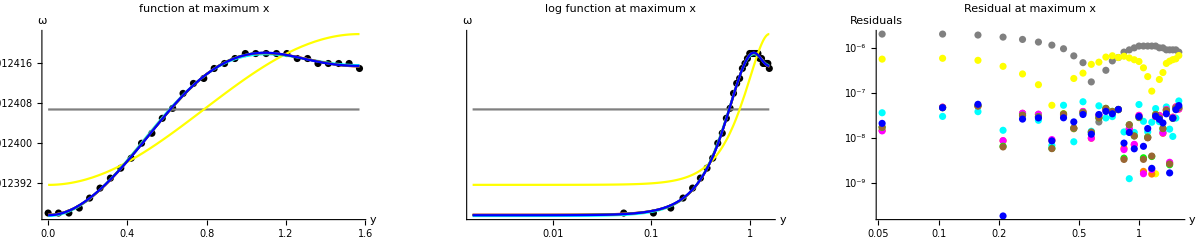

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
maxoXPlot=Table[0,{i,Length[u3maxXFit]+1}];
maxoXPlot[[1]]=ListPlot[maxoYXdata,PlotStyle->Black];
Do[maxoXPlot[[i+1]]=Plot[Normal[u3maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u3maxXFit]}]

maxoXLogPlot=Table[0,{i,Length[u3maxXFit]+1}];
maxoXLogPlot[[1]]=ListLogLogPlot[maxoYXdata,PlotStyle->Black];
Do[maxoXLogPlot[[i+1]]=LogLogPlot[Normal[u3maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u3maxXFit]}]

maxoXRes=Table[0,{i,Length[u3maxXFit]}];
Do[maxoXRes[[i]]=ListLogLogPlot[Transpose[{Ymat[[1;;,maxopos]]//Flatten,Abs[u3maxXFit[[i]]["FitResiduals"]]}],PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u3maxXFit]}]


Show[GraphicsGrid[{{Show[maxoXPlot,AxesLabel->{y,ω},PlotLabel->"function at maximum x",PlotRange->All], Show[maxoXLogPlot,AxesLabel->{y,ω},PlotLabel->"log function at maximum x",PlotRange->All], Show[maxoXRes,AxesLabel->{y,"Residuals"},PlotLabel->"Residual at maximum x",PlotRange->All]}}],ImageSize->1200]
```

The magenta residuals on the right above plot correspond to r=4 which is roughly when the residual no longer improves by adding higher orders

#### x^n Order Determination (local y-fit): Order: y^4 (midpoint estimation)

```mathematica
xN={0,1,2,3,4,5,6,7,8,9,10,11,12,13} 
Ynstr="(LegendreP[0,Cos[y]] aj00 + LegendreP[2,Cos[y]] aj02 + LegendreP[4,Cos[y]] aj04)";
coeffn="{aj00,aj02,aj04}";
Xnstr="(-1+x)^2 x^j";
Ftemp=0;
ctemp = {};
u3XFitFunc={};
u3XcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u3XFitFunc=Join[u3XFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u3XcoeffFitFunc=Join[u3XcoeffFitFunc,{ctemp}],{i,xN}]

u3XFit=Table[0,{i,Length[u3XFitFunc]}];
Do[u3XFit[[i]]=NonlinearModelFit[u3zeta2pts,u3XFitFunc[[i]],u3XcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u3XFit[[i]]["AdjustedRSquared"],16]],{i,Length[u3XFitFunc]}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13}

0.02836268981823499

0.2450008007300331

0.5956447581422903

0.846358759777273

0.956364113003648

0.990467083625583

0.998398414290295

0.999801149747439

0.999983711795706

0.999999238911756

0.999999801217242

0.999999805659069

0.999999821199717

0.999999825455843

Here n=10

{1,16,31}

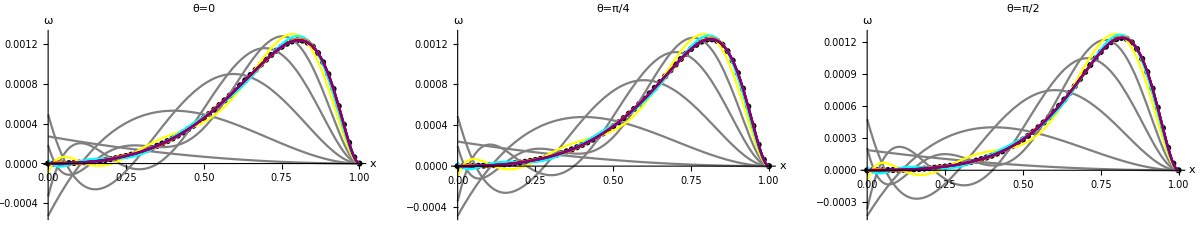

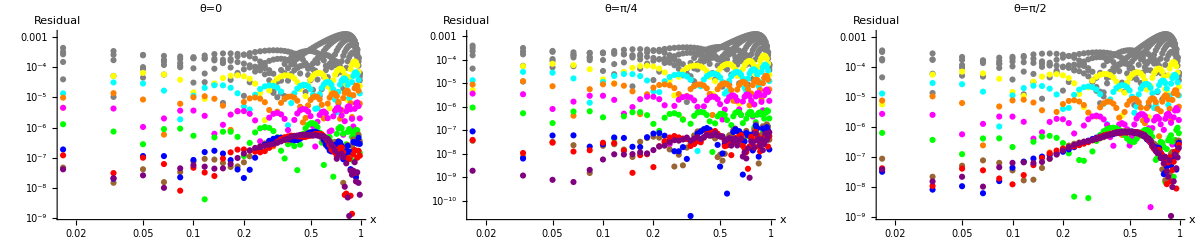

```mathematica
Xcolors={Black,Gray,Gray,Gray,Gray,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u3XPlotY=Table[0,{i,Length[u3XFit]+1},{j,Length[Yplot]}];
Do[u3XPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u3zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u3XPlotY[[i+1,j]]=Plot[u3XFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u3XFit]}]
Show[GraphicsGrid[{{Show[u3XPlotY[[1;;,1]],AxesLabel->{x,ω},PlotLabel->"θ=0",PlotRange->All],Show[u3XPlotY[[1;;,2]],AxesLabel->{x,ω},PlotLabel->"θ=π/4",PlotRange->All],Show[u3XPlotY[[1;;,3]],AxesLabel->{x,ω},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u3XFitRes=Table[0,{i,Length[u3XFit]}];
Do[u3XFitRes[[i]]=Partition[u3XFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u3XFit]}]
u3XResY=Table[0,{i,Length[u3XFit]},{j,Length[Yplot]}];

Do[Do[u3XResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u3XFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u3XFit]}]
Show[GraphicsGrid[{{Show[u3XResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u3XResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u3XResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

Visual verification on bottom-right plot where n=10 is the brown residual

#### y^n Order Determination (global x-fit): Order: x^10

```mathematica
yN={0,2,4,6,8,10,12}
Xnstr="(-1+x)^2(a00j + x^1 a01j + x^2 a02j + x^3 a03j + x^4 a04j + x^5 a05j + x^6 a06j + x^7 a07j + x^8 a08j + x^9 a09j + x^10 a10j)";
coeffn="{a00j,a01j,a02j,a03j,a04j,a05j,a06j,a07j,a08j,a09j,a10j}";
Ynstr="LegendreP[j,Cos[y]]";
Ftemp=0;
ctemp = {};
u3YFitFunc={};
u3YcoeffFitFunc={};

Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u3YFitFunc=Join[u3YFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u3YcoeffFitFunc=Join[u3YcoeffFitFunc,{ctemp}],{i,yN}]
(* To switch between x^n and y^n,  switch u#X... to u#Y... and change Do[...,{i,xN}] to Do[...,{i,yN}] *)

u3YFit=Table[0,{i,Length[u3YFitFunc]}];
Do[u3YFit[[i]]=NonlinearModelFit[u3zeta2pts,u3YFitFunc[[i]],u3YcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u3YFit[[i]]["AdjustedRSquared"],16]],{i,Length[u3YFitFunc]}]
```

{0,2,4,6,8,10,12}

0.996772931129231

0.999969786540609

0.999999801217242

0.999999971268808

0.999999972247577

0.999999972090967

0.999999971924387

n=6

{1,16,31}

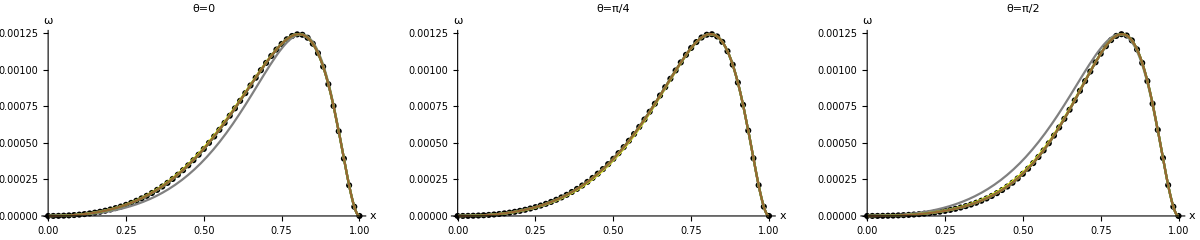

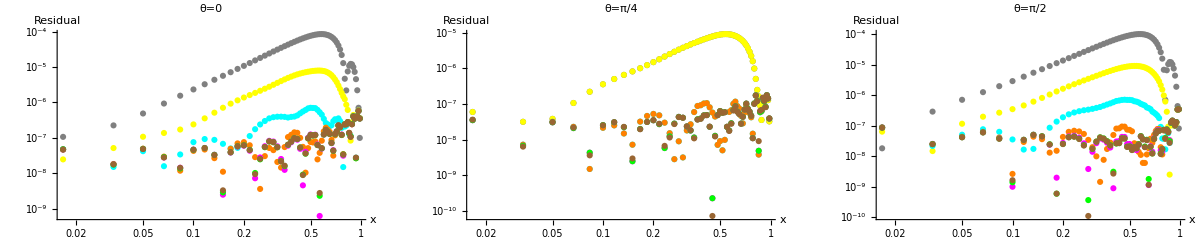

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u3YPlotY=Table[0,{i,Length[u3YFit]+1},{j,Length[Yplot]}];
Do[u3YPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u3zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u3YPlotY[[i+1,j]]=Plot[u3YFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u3YFit]}]
Show[GraphicsGrid[{{Show[u3YPlotY[[1;;,1]],AxesLabel->{x,ω},PlotLabel->"θ=0",PlotRange->All],Show[u3YPlotY[[1;;,2]],AxesLabel->{x,ω},PlotLabel->"θ=π/4",PlotRange->All],Show[u3YPlotY[[1;;,3]],AxesLabel->{x,ω},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u3YFitRes=Table[0,{i,Length[u3YFit]}];
Do[u3YFitRes[[i]]=Partition[u3YFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u3YFit]}]
u3YResY=Table[0,{i,Length[u3YFit]},{j,Length[Yplot]}];
Do[Do[u3YResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u3YFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u3YFit]}]

Show[GraphicsGrid[{{Show[u3YResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u3YResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u3YResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

n=6 is the orange residual

#### Best Fit Calculation: Order: P_6, x^10, u3YFitFunc[[4]]

```mathematica
u3FitFunc=u3YFitFunc[[4]]
u3coeffFitFunc=u3YcoeffFitFunc[[4]];
fullu3fit=NonlinearModelFit[u3zeta2pts,u3FitFunc,u3coeffFitFunc,{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
Normal[fullu3fit];
fullu3fit["BestFitParameters"]
NumberForm[fullu3fit["AdjustedRSquared"],16]
fullu3fit["ParameterTable"];
fullu3fit["ANOVATable"]
```

(-1+x)^2 (a0000+a0100 x+a0200 x^2+a0300 x^3+a0400 x^4+a0500 x^5+a0600 x^6+a0700 x^7+a0800 x^8+a0900 x^9+a1000 x^10)+1/2 (-1+x)^2 (a0002+a0102 x+a0202 x^2+a0302 x^3+a0402 x^4+a0502 x^5+a0602 x^6+a0702 x^7+a0802 x^8+a0902 x^9+a1002 x^10) (-1+3 Cos[y]^2)+1/8 (-1+x)^2 (a0004+a0104 x+a0204 x^2+a0304 x^3+a0404 x^4+a0504 x^5+a0604 x^6+a0704 x^7+a0804 x^8+a0904 x^9+a1004 x^10) (3-30 Cos[y]^2+35 Cos[y]^4)+1/16 (-1+x)^2 (a0006+a0106 x+a0206 x^2+a0306 x^3+a0406 x^4+a0506 x^5+a0606 x^6+a0706 x^7+a0806 x^8+a0906 x^9+a1006 x^10) (-5+105 Cos[y]^2-315 Cos[y]^4+231 Cos[y]^6)

{a0000→2.53193×10^-8,a0100→-0.0000147905,a0200→0.00131467,a0300→-0.0154542,a0400→0.189004,a0500→-1.11218,a0600→4.1593,a0700→-9.52623,a0800→13.4264,a0900→-10.6012,a1000→3.7507,a0002→-2.8806×10^-8,a0102→7.31423×10^-6,a0202→0.0000929464,a0302→0.00248483,a0402→0.0173213,a0502→-0.227132,a0602→1.26746,a0702→-3.62992,a0802→5.77682,a0902→-4.84245,a1002→1.63875,a0004→1.56314×10^-8,a0104→-6.8022×10^-6,a0204→0.000276659,a0304→-0.00621725,a0404→0.0545437,a0504→-0.285713,a0604→0.890944,a0704→-1.69777,a0804→1.92406,a0904→-1.1757,a1004→0.295535,a0006→-1.00528×10^-10,a0106→7.65829×10^-8,a0206→1.4427×10^-6,a0306→0.000139621,a0406→-0.00120187,a0506→0.00769985,a0606→-0.0282668,a0706→0.0630393,a0806→-0.0843233,a0906→0.0607065,a1006→-0.0178112}

0.999999971268808

| DF | SS | MS
Model | 44 | 7.32609×10^6 | 166502.
Error | 1847 | 0.20559 | 0.00011131
Uncorrected Total | 1891 | 7.3261×10^6 | 
Corrected Total | 1890 | 3.58172×10^6 |

#### Best Fit Comparison

```mathematica
u3fitres=Partition[fullu3fit["FitResiduals"],Length[Xrange]];
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]};
u3Plot=Table[0,5,{i,Length[Yplot]}];

Do[u3Plot[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u3zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u3Plot[[2,j]]=Plot[fullu3fit["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u3Plot[[3,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u3zeta2[[Yplot[[j]],1;;]]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u3Plot[[4,j]]=LogLogPlot[Abs[fullu3fit["Function"][Yrange[[Yplot[[j]]]],x]],{x,0.01,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u3Plot[[5,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u3fitres[[Yplot[[j]],1;;]]]}],PlotStyle->Red],{j,Length[Yplot]}];
```

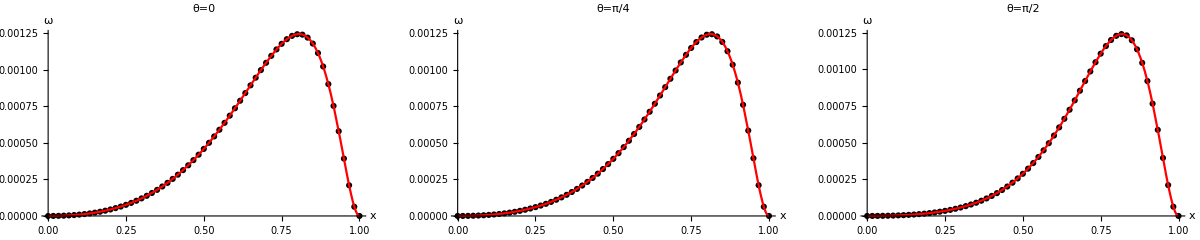

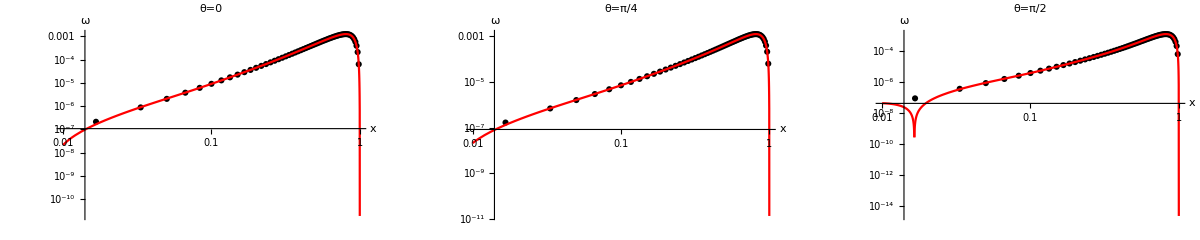

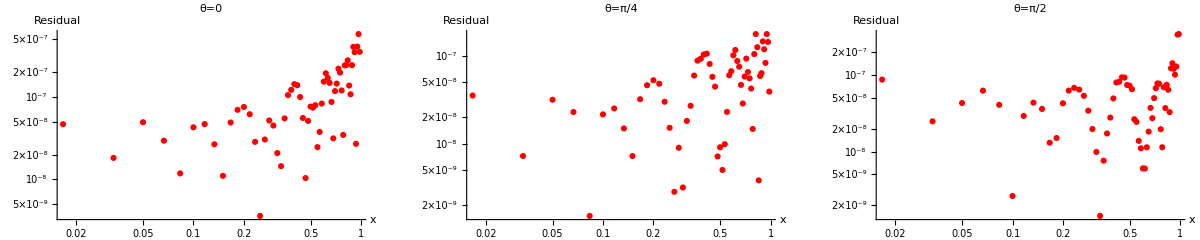

```mathematica
Show[GraphicsGrid[{{Show[u3Plot[[1;;2,1]],AxesLabel->{x,ω},PlotLabel->"θ=0",PlotRange->All],Show[u3Plot[[1;;2,2]],AxesLabel->{x,ω},PlotLabel->"θ=π/4",PlotRange->All],Show[u3Plot[[1;;2,3]],AxesLabel->{x,ω},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u3Plot[[3;;4,1]],AxesLabel->{x,ω},PlotLabel->"θ=0",PlotRange->All],Show[u3Plot[[3;;4,2]],AxesLabel->{x,ω},PlotLabel->"θ=π/4",PlotRange->All],Show[u3Plot[[3;;4,3]],AxesLabel->{x,ω},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u3Plot[[5,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All],Show[u3Plot[[5,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All],Show[u3Plot[[5,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

### ψ ζ^2 Fitting

#### y^n Order Determination: Local x(midpoint) location

{1}

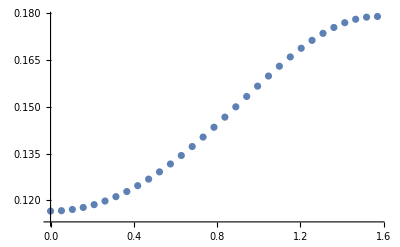

{0,2,4,6,8,10,12,14}

0.976250755784736

0.999881066847768

0.999999322432608

0.999999993436899

0.999999999434437

0.999999999604921

0.999999999597073

0.999999999606886

```mathematica
maxppos=Ordering[Abs[u4zeta2[[Length[Yrange],1;;]]],-1]
maxpYXdata=Transpose[{Ymat[[1;;,maxppos]]//Flatten,u4zeta2[[1;;,maxppos]]//Flatten}];
ListPlot[maxpYXdata]
yN={0,2,4,6,8,10,12,14}
Ynstr="yj LegendreP[j,Cos[y]]";
coeffn="{yj}";
Ftemp=0;
ctemp = {};
u4maxXFitFunc={};
u4maxXcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]];coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp; u4maxXFitFunc=Join[u4maxXFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u4maxXcoeffFitFunc=Join[u4maxXcoeffFitFunc,{ctemp}],{i,yN}]

u4maxXFit=Table[0,{i,Length[u4maxXFitFunc]}];
Do[u4maxXFit[[i]]=NonlinearModelFit[maxpYXdata,u4maxXFitFunc[[i]],u4maxXcoeffFitFunc[[i]],{y},PrecisionGoal->5,AccuracyGoal->5]; Print[NumberForm[u4maxXFit[[i]]["AdjustedRSquared"],16]],{i,Length[u4maxXFitFunc]}]
```

From this we notice that the R^2value saturates at n=6, with R^2=0.999999993436899

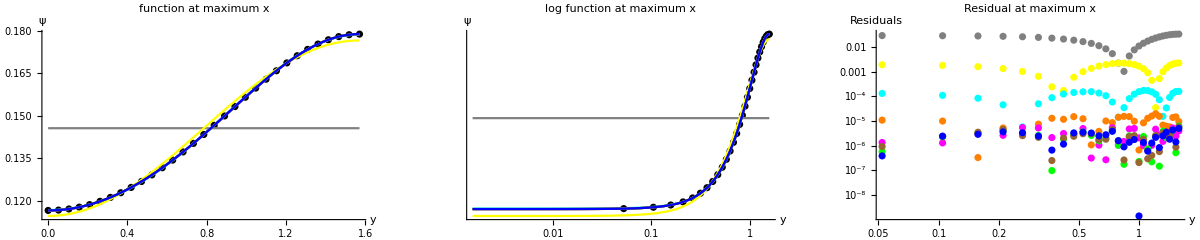

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
maxpXPlot=Table[0,{i,Length[u4maxXFit]+1}];
maxpXPlot[[1]]=ListPlot[maxpYXdata,PlotStyle->Black];
Do[maxpXPlot[[i+1]]=Plot[Normal[u4maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u4maxXFit]}]

maxpXLogPlot=Table[0,{i,Length[u4maxXFit]+1}];
maxpXLogPlot[[1]]=ListLogLogPlot[maxpYXdata,PlotStyle->Black];
Do[maxpXLogPlot[[i+1]]=LogLogPlot[Normal[u4maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u4maxXFit]}]

maxpXRes=Table[0,{i,Length[u4maxXFit]}];
Do[maxpXRes[[i]]=ListLogLogPlot[Transpose[{Ymat[[1;;,maxppos]]//Flatten,Abs[u4maxXFit[[i]]["FitResiduals"]]}],PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u4maxXFit]}]


Show[GraphicsGrid[{{Show[maxpXPlot,AxesLabel->{y,ψ},PlotLabel->"function at maximum x",PlotRange->All], Show[maxpXLogPlot,AxesLabel->{y,ψ},PlotLabel->"log function at maximum x",PlotRange->All], Show[maxpXRes,AxesLabel->{y,"Residuals"},PlotLabel->"Residual at maximum x",PlotRange->All]}}],ImageSize->1200]
```

The magenta residuals on the right above plot correspond to r=8 which is roughly when the residual no longer improves by adding higher orders

#### x^n Order Determination (local y-fit): Order: y^8 (midpoint estimation)

```mathematica
xN={0,1,2,3,4,5,6,7,8,9,10,11,12,13} 
Ynstr="(LegendreP[0,Cos[y]] aj00 + LegendreP[2,Cos[y]] aj02 + LegendreP[4,Cos[y]] aj04 + LegendreP[6,Cos[y]] aj06 + LegendreP[8,Cos[y]] aj08)";
coeffn="{aj00,aj02,aj04,aj06,aj08}";
Xnstr="(-1+x) x^j";
Ftemp=0;
ctemp = {};
u4XFitFunc={};
u4XcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u4XFitFunc=Join[u4XFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u4XcoeffFitFunc=Join[u4XcoeffFitFunc,{ctemp}],{i,xN}]

u4XFit=Table[0,{i,Length[u4XFitFunc]}];
Do[u4XFit[[i]]=NonlinearModelFit[u4zeta2pts,u4XFitFunc[[i]],u4XcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u4XFit[[i]]["AdjustedRSquared"],16]],{i,Length[u4XFitFunc]}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13}

0.945161672811461

0.998556234335818

0.999956986190531

0.999980572975457

0.999995370263149

0.999999485709022

0.999999974576554

0.999999993699884

0.999999996231254

0.999999998617242

0.999999999406804

0.999999999523821

0.999999999533958

0.999999999534744

Here n=10

{1,16,31}

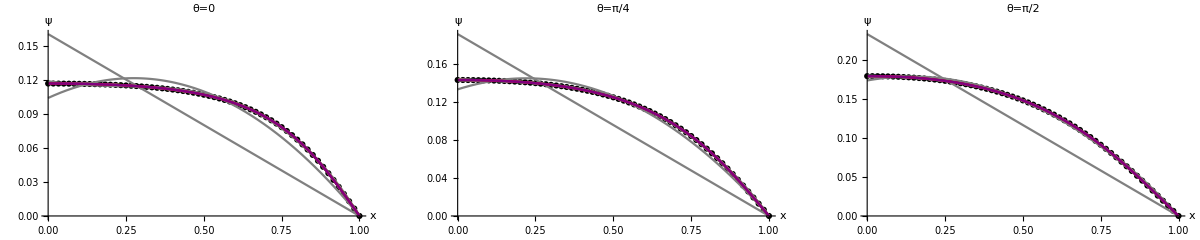

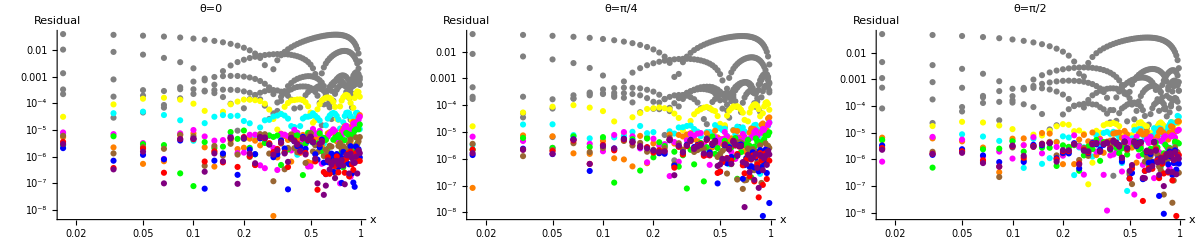

```mathematica
Xcolors={Black,Gray,Gray,Gray,Gray,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u4XPlotY=Table[0,{i,Length[u4XFit]+1},{j,Length[Yplot]}];
Do[u4XPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u4zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u4XPlotY[[i+1,j]]=Plot[u4XFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u4XFit]}]
Show[GraphicsGrid[{{Show[u4XPlotY[[1;;,1]],AxesLabel->{x,ψ},PlotLabel->"θ=0",PlotRange->All],Show[u4XPlotY[[1;;,2]],AxesLabel->{x,ψ},PlotLabel->"θ=π/4",PlotRange->All],Show[u4XPlotY[[1;;,3]],AxesLabel->{x,ψ},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u4XFitRes=Table[0,{i,Length[u4XFit]}];
Do[u4XFitRes[[i]]=Partition[u4XFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u4XFit]}]
u4XResY=Table[0,{i,Length[u4XFit]},{j,Length[Yplot]}];

Do[Do[u4XResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u4XFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u4XFit]}]
Show[GraphicsGrid[{{Show[u4XResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u4XResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u4XResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

Visual verification on bottom-right plot where n=10 is the brown residual

#### y^n Order Determination (global x-fit): Order: x^10

```mathematica
yN={0,2,4,6,8,10,12}
Xnstr="(-1+x)(a00j + x^1 a01j + x^2 a02j + x^3 a03j + x^4 a04j + x^5 a05j + x^6 a06j + x^7 a07j + x^8 a08j + x^9 a09j + x^(10) a10j)";
coeffn="{a00j,a01j,a02j,a03j,a04j,a05j,a06j,a07j,a08j,a09j,a10j}";
Ynstr="LegendreP[j,Cos[y]]";
Ftemp=0;
ctemp = {};
u4YFitFunc={};
u4YcoeffFitFunc={};

Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u4YFitFunc=Join[u4YFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u4YcoeffFitFunc=Join[u4YcoeffFitFunc,{ctemp}],{i,yN}]
(* To switch between x^n and y^n,  switch u#X... to u#Y... and change Do[...,{i,xN}] to Do[...,{i,yN}] *)

u4YFit=Table[0,{i,Length[u4YFitFunc]}];
Do[u4YFit[[i]]=NonlinearModelFit[u4zeta2pts,u4YFitFunc[[i]],u4YcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u4YFit[[i]]["AdjustedRSquared"],16]],{i,Length[u4YFitFunc]}]
```

{0,2,4,6,8,10,12}

0.983003970476109

0.999930425442644

0.999999668034281

0.999999996997287

0.999999999406804

0.999999999426284

0.999999999423871

This is just verification, we determined y^8 was the saturation point only from a fit at the location where u_0 was maximum. So in that case we had a 1-dimensional fit to make. In this case, we find the y^n value for a global fit on the x-dimension. We find that the global saturation residual is n=8

{1,16,31}

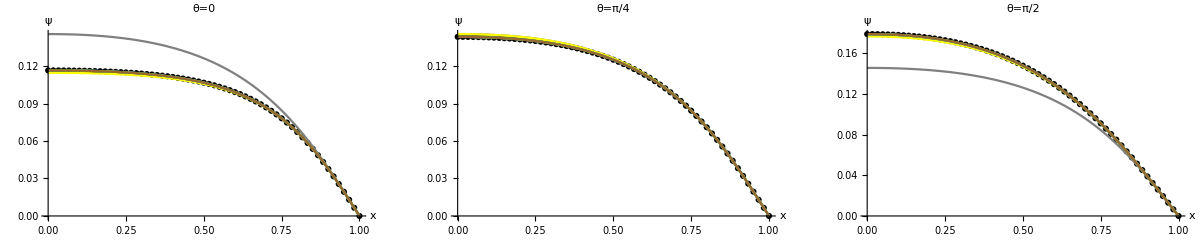

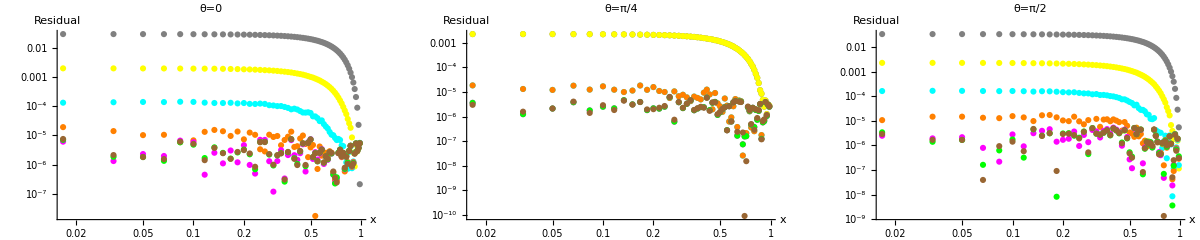

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u4YPlotY=Table[0,{i,Length[u4YFit]+1},{j,Length[Yplot]}];
Do[u4YPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u4zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u4YPlotY[[i+1,j]]=Plot[u4YFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u4YFit]}]
Show[GraphicsGrid[{{Show[u4YPlotY[[1;;,1]],AxesLabel->{x,ψ},PlotLabel->"θ=0",PlotRange->All],Show[u4YPlotY[[1;;,2]],AxesLabel->{x,ψ},PlotLabel->"θ=π/4",PlotRange->All],Show[u4YPlotY[[1;;,3]],AxesLabel->{x,ψ},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u4YFitRes=Table[0,{i,Length[u4YFit]}];
Do[u4YFitRes[[i]]=Partition[u4YFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u4YFit]}]
u4YResY=Table[0,{i,Length[u4YFit]},{j,Length[Yplot]}];
Do[Do[u4YResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u4YFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u4YFit]}]

Show[GraphicsGrid[{{Show[u4YResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u4YResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u4YResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

As explained above, n=8 is the magenta residual

#### Best Fit Calculation: Order: P_8, x^8, u4YFitFunc[[5]]

```mathematica
u4FitFunc=u4YFitFunc[[5]]
u4coeffFitFunc=u4YcoeffFitFunc[[5]];
fullu4fit=NonlinearModelFit[u4zeta2pts,u4FitFunc,u4coeffFitFunc,{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
Normal[fullu4fit];
fullu4fit["BestFitParameters"]
NumberForm[fullu4fit["AdjustedRSquared"],16]
fullu4fit["ParameterTable"];
fullu4fit["ANOVATable"]
```

(-1+x) (a0000+a0100 x+a0200 x^2+a0300 x^3+a0400 x^4+a0500 x^5+a0600 x^6+a0700 x^7+a0800 x^8+a0900 x^9+a1000 x^10)+1/2 (-1+x) (a0002+a0102 x+a0202 x^2+a0302 x^3+a0402 x^4+a0502 x^5+a0602 x^6+a0702 x^7+a0802 x^8+a0902 x^9+a1002 x^10) (-1+3 Cos[y]^2)+1/8 (-1+x) (a0004+a0104 x+a0204 x^2+a0304 x^3+a0404 x^4+a0504 x^5+a0604 x^6+a0704 x^7+a0804 x^8+a0904 x^9+a1004 x^10) (3-30 Cos[y]^2+35 Cos[y]^4)+1/16 (-1+x) (a0006+a0106 x+a0206 x^2+a0306 x^3+a0406 x^4+a0506 x^5+a0606 x^6+a0706 x^7+a0806 x^8+a0906 x^9+a1006 x^10) (-5+105 Cos[y]^2-315 Cos[y]^4+231 Cos[y]^6)+1/128 (-1+x) (a0008+a0108 x+a0208 x^2+a0308 x^3+a0408 x^4+a0508 x^5+a0608 x^6+a0708 x^7+a0808 x^8+a0908 x^9+a1008 x^10) (35-1260 Cos[y]^2+6930 Cos[y]^4-12012 Cos[y]^6+6435 Cos[y]^8)

{a0000→-0.155761,a0100→-0.155418,a0200→-0.118024,a0300→0.199885,a0400→-2.08093,a0500→9.76568,a0600→-27.9346,a0700→49.3643,a0800→-52.5116,a0900→30.8916,a1000→-7.65499,a0002→0.0429555,a0102→0.0433346,a0202→-0.0101632,a0302→0.189661,a0402→-1.82765,a0502→8.1138,a0602→-22.8593,a0702→39.4968,a0802→-41.107,a0902→23.4725,a1002→-5.55453,a0004→-0.00410264,a0104→-0.0042691,a0204→0.00557292,a0304→-0.0236699,a0404→0.156567,a0504→-0.383907,a0604→0.577543,a0704→-0.484308,a0804→0.204703,a0904→-0.089534,a1004→0.0454975,a0006→0.000372076,a0106→0.000403001,a0206→-0.00415335,a0306→0.065658,a0406→-0.522265,a0506→2.19329,a0606→-5.44827,a0706→8.23053,a0806→-7.40749,a0906→3.65106,a1006→-0.759164,a0008→-0.0000374145,a0108→5.23377×10^-6,a0208→0.00147636,a0308→-0.0415847,a0408→0.374795,a0508→-1.6657,a0608→4.21919,a0708→-6.38462,a0808→5.71262,a0908→-2.78907,a1008→0.572925}

0.999999999406804

General::munfl: Exp[-13873.3] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5545.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-10279.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| DF | SS | MS
Model | 55 | 2.58079×10^11 | 4.69234×10^9
Error | 1836 | 148.639 | 0.0809579
Uncorrected Total | 1891 | 2.58079×10^11 | 
Corrected Total | 1890 | 3.79703×10^10 |

#### Best Fit Comparison

```mathematica
u4fitres=Partition[fullu4fit["FitResiduals"],Length[Xrange]];
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]};
u4Plot=Table[0,5,{i,Length[Yplot]}];

Do[u4Plot[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u4zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u4Plot[[2,j]]=Plot[fullu4fit["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u4Plot[[3,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u4zeta2[[Yplot[[j]],1;;]]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u4Plot[[4,j]]=LogLogPlot[Abs[fullu4fit["Function"][Yrange[[Yplot[[j]]]],x]],{x,0.01,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u4Plot[[5,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u4fitres[[Yplot[[j]],1;;]]]}],PlotStyle->Red],{j,Length[Yplot]}];
```

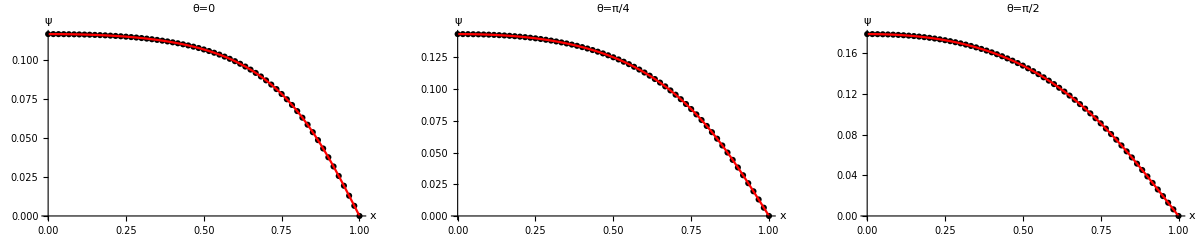

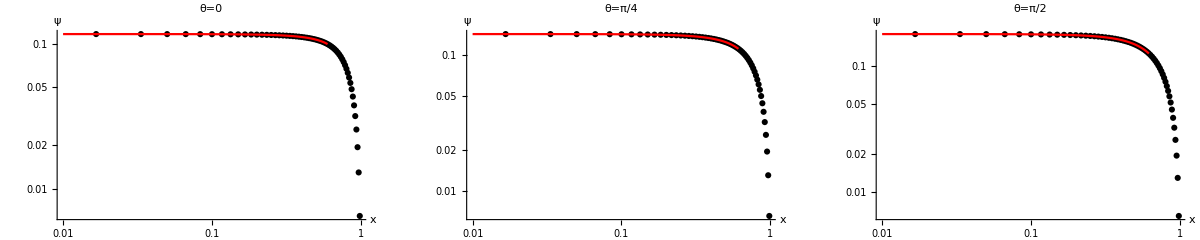

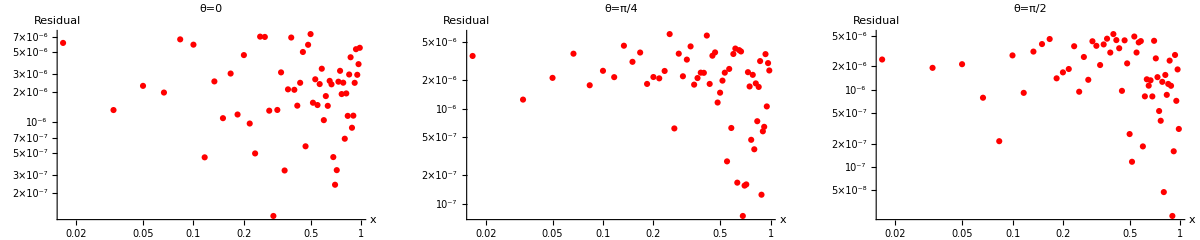

```mathematica
Show[GraphicsGrid[{{Show[u4Plot[[1;;2,1]],AxesLabel->{x,ψ},PlotLabel->"θ=0",PlotRange->All],Show[u4Plot[[1;;2,2]],AxesLabel->{x,ψ},PlotLabel->"θ=π/4",PlotRange->All],Show[u4Plot[[1;;2,3]],AxesLabel->{x,ψ},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u4Plot[[3;;4,1]],AxesLabel->{x,ψ},PlotLabel->"θ=0",PlotRange->All],Show[u4Plot[[3;;4,2]],AxesLabel->{x,ψ},PlotLabel->"θ=π/4",PlotRange->All],Show[u4Plot[[3;;4,3]],AxesLabel->{x,ψ},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u4Plot[[5,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All],Show[u4Plot[[5,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All],Show[u4Plot[[5,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

## Export

### Fit export

```mathematica
Export["ExponentialFitXmatout.dat",Transpose[Xmat]];
Export["ExponentialFitYmatout.dat",Transpose[Ymat]];
Export["ExponentialFitu0out.dat",Transpose[fullu0fit["Function"][Ymat,Xmat]]];
Export["ExponentialFitu1out.dat",Transpose[fullu1fit["Function"][Ymat,Xmat]]];
Export["ExponentialFitu2out.dat",Transpose[fullu2fit["Function"][Ymat,Xmat]]];
Export["ExponentialFitu3out.dat",Transpose[fullu3fit["Function"][Ymat,Xmat]]];
Export["ExponentialFitu4out.dat",Transpose[fullu4fit["Function"][Ymat,Xmat]]];

Export["ExponentialFitout.dat",Transpose[{Xmat[[Yplot[[1]],1;;]],
u0zeta2[[Yplot[[1]],1;;]],fullu0fit["Function"][Yrange[[Yplot[[1]]]],Xmat[[Yplot[[1]],1;;]]],
Abs[u0fitres[[Yplot[[1]],1;;]]],
u1zeta2[[Yplot[[1]],1;;]],fullu1fit["Function"][Yrange[[Yplot[[1]]]],Xmat[[Yplot[[1]],1;;]]],
Abs[u1fitres[[Yplot[[1]],1;;]]],
u2zeta2[[Yplot[[1]],1;;]],fullu2fit["Function"][Yrange[[Yplot[[1]]]],Xmat[[Yplot[[1]],1;;]]],
Abs[u2fitres[[Yplot[[1]],1;;]]],
u3zeta2[[Yplot[[1]],1;;]],fullu3fit["Function"][Yrange[[Yplot[[1]]]],Xmat[[Yplot[[1]],1;;]]],
Abs[u3fitres[[Yplot[[1]],1;;]]],
u4zeta2[[Yplot[[1]],1;;]],fullu4fit["Function"][Yrange[[Yplot[[1]]]],Xmat[[Yplot[[1]],1;;]]],
Abs[u4fitres[[Yplot[[1]],1;;]]],
u0zeta2[[Yplot[[2]],1;;]],fullu0fit["Function"][Yrange[[Yplot[[2]]]],Xmat[[Yplot[[2]],1;;]]],
Abs[u0fitres[[Yplot[[2]],1;;]]],
u1zeta2[[Yplot[[2]],1;;]],fullu1fit["Function"][Yrange[[Yplot[[2]]]],Xmat[[Yplot[[2]],1;;]]],
Abs[u1fitres[[Yplot[[2]],1;;]]],
u2zeta2[[Yplot[[2]],1;;]],fullu2fit["Function"][Yrange[[Yplot[[2]]]],Xmat[[Yplot[[2]],1;;]]],
Abs[u2fitres[[Yplot[[2]],1;;]]],
u3zeta2[[Yplot[[2]],1;;]],fullu3fit["Function"][Yrange[[Yplot[[2]]]],Xmat[[Yplot[[2]],1;;]]],
Abs[u3fitres[[Yplot[[2]],1;;]]],
u4zeta2[[Yplot[[2]],1;;]],fullu4fit["Function"][Yrange[[Yplot[[2]]]],Xmat[[Yplot[[2]],1;;]]],
Abs[u4fitres[[Yplot[[2]],1;;]]],
u0zeta2[[Yplot[[3]],1;;]],fullu0fit["Function"][Yrange[[Yplot[[3]]]],Xmat[[Yplot[[3]],1;;]]],
Abs[u0fitres[[Yplot[[3]],1;;]]],
u1zeta2[[Yplot[[3]],1;;]],fullu1fit["Function"][Yrange[[Yplot[[3]]]],Xmat[[Yplot[[3]],1;;]]],
Abs[u1fitres[[Yplot[[3]],1;;]]],
u2zeta2[[Yplot[[3]],1;;]],fullu2fit["Function"][Yrange[[Yplot[[3]]]],Xmat[[Yplot[[3]],1;;]]],
Abs[u2fitres[[Yplot[[3]],1;;]]],
u3zeta2[[Yplot[[3]],1;;]],fullu3fit["Function"][Yrange[[Yplot[[3]]]],Xmat[[Yplot[[3]],1;;]]],
Abs[u3fitres[[Yplot[[3]],1;;]]],
u4zeta2[[Yplot[[3]],1;;]],fullu4fit["Function"][Yrange[[Yplot[[3]]]],Xmat[[Yplot[[3]],1;;]]],
Abs[u4fitres[[Yplot[[3]],1;;]]]}]];
```

## Fit Export

```mathematica
EXPu0export=fullu0fit["BestFitParameters"];
EXPu1export=fullu1fit["BestFitParameters"];
EXPu2export=fullu2fit["BestFitParameters"];
EXPu3export=fullu3fit["BestFitParameters"];
EXPu4export=fullu4fit["BestFitParameters"];

For[i=1,i<=Length[EXPu1export],i++,EXPu1export[[i]]=ToExpression[StringReplace[ToString[EXPu1export[[i]],FormatType->StandardForm],"a"->"b"]]]

For[i=1,i<=Length[EXPu2export],i++,EXPu2export[[i]]=ToExpression[StringReplace[ToString[EXPu2export[[i]],FormatType->StandardForm],"a"->"c"]]]

For[i=1,i<=Length[EXPu3export],i++,EXPu3export[[i]]=ToExpression[StringReplace[ToString[EXPu3export[[i]],FormatType->StandardForm],"a"->"d"]]]

For[i=1,i<=Length[EXPu4export],i++,EXPu4export[[i]]=ToExpression[StringReplace[ToString[EXPu4export[[i]],FormatType->StandardForm],"a"->"e"]]]
```

```mathematica
Export["EXPu0FitCoeffs.mx",EXPu0export]
Export["EXPu1FitCoeffs.mx",EXPu1export]
Export["EXPu2FitCoeffs.mx",EXPu2export]
Export["EXPu3FitCoeffs.mx",EXPu3export]
Export["EXPu4FitCoeffs.mx",EXPu4export]
```

EXPu0FitCoeffs.mx

EXPu1FitCoeffs.mx

EXPu2FitCoeffs.mx

EXPu3FitCoeffs.mx

EXPu4FitCoeffs.mx

```mathematica
Import["EXPu0FitCoeffs.mx"]
Import["EXPu1FitCoeffs.mx"]
Import["EXPu2FitCoeffs.mx"]
Import["EXPu3FitCoeffs.mx"]
Import["EXPu4FitCoeffs.mx"]
```

{a0000→0.00259415,a0100→-0.00838604,a0200→0.276629,a0300→-2.99656,a0400→20.8909,a0500→-95.7186,a0600→300.938,a0700→-658.781,a0800→1003.93,a0900→-1044.44,a1000→707.438,a1100→-281.127,a1200→49.6745,a0002→-0.000646711,a0102→0.0000692154,a0202→-0.0245956,a0302→0.203645,a0402→-1.15033,a0502→4.04693,a0602→-9.32451,a0702→13.9145,a0802→-12.947,a0902→6.93172,a1002→-1.94175,a1102→0.543771,a1202→-0.251764,a0004→0.000199077,a0104→-0.000721655,a0204→0.0215893,a0304→-0.229595,a0404→1.5296,a0504→-6.72759,a0604→20.2102,a0704→-42.1455,a0804→60.9249,a0904→-59.8637,a1004→38.1174,a1104→-14.165,a1204→2.32819,a0006→-0.0000229613,a0106→-0.000117178,a0206→0.000617218,a0306→0.00015902,a0406→-0.0426082,a0506→0.34787,a0606→-1.4421,a0706→3.66418,a0806→-6.0181,a0906→6.42987,a1006→-4.33057,a1106→1.67548,a1206→-0.284655,a0008→-3.08651×10^-6,a0108→0.000285419,a0208→-0.0051789,a0308→0.0517026,a0408→-0.315757,a0508→1.25767,a0608→-3.38108,a0708→6.21703,a0808→-7.78542,a0908→6.47877,a1008→-3.38906,a1108→0.990376,a1208→-0.119322}

{b0000→-0.0313518,b0100→-0.0567903,b0200→0.267201,b0300→-1.98868,b0400→7.18225,b0500→-16.1566,b0600→21.4264,b0700→-15.7182,b0800→4.91785,b0002→0.0287121,b0102→0.0351248,b0202→-0.0522703,b0302→0.472036,b0402→-1.6461,b0502→3.626,b0602→-4.76372,b0702→3.49212,b0802→-1.10998,b0004→-0.00645619,b0104→-0.00592775,b0204→0.000831269,b0304→-0.00290039,b0404→0.181476,b0504→-0.627386,b0604→1.19946,b0704→-1.15238,b0804→0.41371,b0006→0.000837572,b0106→0.0000462419,b0206→0.00850046,b0306→-0.0607549,b0406→0.201857,b0506→-0.4223,b0606→0.505433,b0706→-0.304366,b0806→0.0706748,b0008→-0.0000953757,b0108→0.0000788313,b0208→-0.00193405,b0308→0.0132203,b0408→-0.0445096,b0508→0.0946676,b0608→-0.121257,b0708→0.0825362,b0808→-0.0227201}

{c0000→-0.00548602,c0100→-0.00467957,c0200→-0.0197624,c0300→-0.104526,c0400→0.474557,c0500→-1.76565,c0600→3.15385,c0700→-2.99838,c0800→1.1943,c0002→-0.00435205,c0102→-0.0232348,c0202→0.232356,c0302→-1.38482,c0402→5.16253,c0502→-11.2538,c0602→14.6019,c0702→-10.3942,c0802→3.06422,c0004→0.00186954,c0104→-0.00240962,c0204→0.0446135,c0304→-0.285972,c0404→0.932484,c0504→-1.86245,c0604→2.14705,c0704→-1.26597,c0804→0.290487,c0006→-0.000341898,c0106→0.000163555,c0206→-0.00527038,c0306→0.0389667,c0406→-0.135736,c0506→0.299297,c0606→-0.393488,c0706→0.270871,c0806→-0.0744744,c0008→0.0000459743,c0108→0.0000522349,c0208→-0.000138754,c0308→-0.000577628,c0408→0.00236166,c0508→-0.00815646,c0608→0.0165649,c0708→-0.0151878,c0808→0.00503759}

{d0000→2.53193×10^-8,d0100→-0.0000147905,d0200→0.00131467,d0300→-0.0154542,d0400→0.189004,d0500→-1.11218,d0600→4.1593,d0700→-9.52623,d0800→13.4264,d0900→-10.6012,d1000→3.7507,d0002→-2.8806×10^-8,d0102→7.31423×10^-6,d0202→0.0000929464,d0302→0.00248483,d0402→0.0173213,d0502→-0.227132,d0602→1.26746,d0702→-3.62992,d0802→5.77682,d0902→-4.84245,d1002→1.63875,d0004→1.56314×10^-8,d0104→-6.8022×10^-6,d0204→0.000276659,d0304→-0.00621725,d0404→0.0545437,d0504→-0.285713,d0604→0.890944,d0704→-1.69777,d0804→1.92406,d0904→-1.1757,d1004→0.295535,d0006→-1.00528×10^-10,d0106→7.65829×10^-8,d0206→1.4427×10^-6,d0306→0.000139621,d0406→-0.00120187,d0506→0.00769985,d0606→-0.0282668,d0706→0.0630393,d0806→-0.0843233,d0906→0.0607065,d1006→-0.0178112}

{e0000→-0.155761,e0100→-0.155418,e0200→-0.118024,e0300→0.199885,e0400→-2.08093,e0500→9.76568,e0600→-27.9346,e0700→49.3643,e0800→-52.5116,e0900→30.8916,e1000→-7.65499,e0002→0.0429555,e0102→0.0433346,e0202→-0.0101632,e0302→0.189661,e0402→-1.82765,e0502→8.1138,e0602→-22.8593,e0702→39.4968,e0802→-41.107,e0902→23.4725,e1002→-5.55453,e0004→-0.00410264,e0104→-0.0042691,e0204→0.00557292,e0304→-0.0236699,e0404→0.156567,e0504→-0.383907,e0604→0.577543,e0704→-0.484308,e0804→0.204703,e0904→-0.089534,e1004→0.0454975,e0006→0.000372076,e0106→0.000403001,e0206→-0.00415335,e0306→0.065658,e0406→-0.522265,e0506→2.19329,e0606→-5.44827,e0706→8.23053,e0806→-7.40749,e0906→3.65106,e1006→-0.759164,e0008→-0.0000374145,e0108→5.23377×10^-6,e0208→0.00147636,e0308→-0.0415847,e0408→0.374795,e0508→-1.6657,e0608→4.21919,e0708→-6.38462,e0808→5.71262,e0908→-2.78907,e1008→0.572925}